## Convergencia numérica

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Paquetes a importar

```mathematica
Needs["MaTeX`"] (*Importa la paquetería de LaTeX*)
SetOptions[MaTeX, "Preamble" -> {"\\usepackage{xcolor}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
(*Directorio donde están las paqueterías*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Programas\\Packages"]

Needs["MieTheory`"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Programas\Packages

```mathematica
<< "MieTheory.wl"
```

```mathematica
cp=ResourceFunction["CombinePlots"];
```

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
hbar=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=299792458*^9 (*nm s^-1*)(*Velocidad de la luz*);

omega10=Range[0,10,0.01]; 
omegaVis=Range[2,3.1,0.01];
energyTicksMajorVisible={2.07,2.26,2.48,2.76,3.1};

epsPlasma=1.823;


(*Colores*)
blueUNAM=RGBColor[6/255,151/255,213/255];
redUNAM=RGBColor[232/255,68/255,42/255];
gris=RGBColor[127/255,146/255,151/255];
bluelight30=RGBColor[0/255,170/255,212/255];
bluedark30=RGBColor[0/255,51/255,128/255];
greenlight30=RGBColor[137/255,160/255,44/255];
greendark30=RGBColor[68/255,80/255,22/255];
bluemedium30=RGBColor[55/255,171/255,200/255];
redlight34=RGBColor[255/255,42/255,42/255];
reddark34=RGBColor[128/255,0/255,0/255];
colorsCHCM={bluelight30,bluedark30,bluemedium30,redlight34,reddark34,greenlight30,greendark30}
colors2={blueUNAM, redUNAM};
colors={Blue,Red};
color5={Orange};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
rojos=Table[RGBColor[1,g,0],{g,0,0.9,0.16}]
sunsetColors=Table[ColorData["SunsetColors"][i],{i,0,0.8,1/7}]
solarColors=Table[ColorData["SolarColors"][i],{i,0,0.8,1/7}]
alpineColors=Table[ColorData["AlpineColors"][i],{i,0,0.8,1/7}]
lakeColors=Table[ColorData["LakeColors"][i],{i,0,0.8,1/7}]
candyColors=Table[ColorData["CandyColors"][i],{i,0,0.8,1/7}]
verde=RGBColor[150/255,200/255,60/255];


lajolla = ColorMapSuite["lajolla"];
```

{RGBColor[0, Rational[2, 3], Rational[212, 255]],RGBColor[0, Rational[1, 5], Rational[128, 255]],RGBColor[Rational[11, 51], Rational[57, 85], Rational[40, 51]],RGBColor[1, Rational[14, 85], Rational[14, 85]],RGBColor[Rational[128, 255], 0, 0],RGBColor[Rational[137, 255], Rational[32, 51], Rational[44, 255]],RGBColor[Rational[4, 15], Rational[16, 51], Rational[22, 255]]}

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{RGBColor[1, 0., 0],RGBColor[1, 0.16, 0],RGBColor[1, 0.32, 0],RGBColor[1, 0.48, 0],RGBColor[1, 0.64, 0],RGBColor[1, 0.8, 0]}

{RGBColor[0., 0., 0.],RGBColor[0.3195368571428571, 0.1164, 0.4341454285714286],RGBColor[0.6695744285714286, 0.22438285714285713, 0.338128],RGBColor[0.8974812857142858, 0.3693308571428571, 0.1452665142857143],RGBColor[0.9882154285714286, 0.5505617142857143, 0.08483494285714285],RGBColor[1., 0.7397017142857143, 0.23300614285714283]}

{RGBColor[0.468742, 0., 0.0158236],RGBColor[0.6706774285714285, 0.06984285714285714, 0.009042057142857144],RGBColor[0.8432481428571429, 0.15849014285714286, 0.008003357142857142],RGBColor[0.9277247142857143, 0.30355071428571423, 0.024193185714285713],RGBColor[0.978545, 0.4534661428571428, 0.0459689],RGBColor[0.995709, 0.6082364285714286, 0.07333049999999999]}

{RGBColor[0.277546, 0.355398, 0.484215],RGBColor[0.3092687142857143, 0.43180485714285716, 0.45451742857142857],RGBColor[0.35382528571428573, 0.4807017142857143, 0.3698534285714286],RGBColor[0.43932542857142853, 0.5335538571428571, 0.38461414285714285],RGBColor[0.5610134285714286, 0.5994675714285714, 0.49026099999999995],RGBColor[0.6995328571428572, 0.6994642857142856, 0.6226554285714285]}

{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.40930385714285716, 0.25890179999999996, 0.6923064285714285],RGBColor[0.5251917142857143, 0.46039919999999995, 0.8552008571428571],RGBColor[0.6206238571428572, 0.6188315714285714, 0.9107938571428571],RGBColor[0.7058281428571428, 0.7557314285714285, 0.9127361428571429],RGBColor[0.7881374285714285, 0.8555037142857143, 0.9026041428571429]}

{RGBColor[0.405188, 0.204349, 0.343389],RGBColor[0.6033010000000001, 0.22473442857142858, 0.36270257142857143],RGBColor[0.7647998571428571, 0.3022755714285714, 0.4413708571428571],RGBColor[0.8306595714285715, 0.45290014285714286, 0.5840857142857143],RGBColor[0.7940618571428572, 0.5946167142857143, 0.7287942857142857],RGBColor[0.7161124285714285, 0.7039788571428571, 0.8368194285714285]}

## Funciones

```mathematica
dataQext[dataCabs_,dataCsca_]:=Module[{dataCext},
dataCext=Transpose[{dataCabs[[All,1]],dataCabs[[All,2]]+dataCsca[[All,2]]}]]

errorAbs[data1_,data2_]:=Module[{error},
error=Abs[data1-data2]]

errorRel[data1_,data2_]:=Module[{error},
error=100*Abs[data1-data2]/data2]
```

## Gráficas

```mathematica
plotStyling = {PlotRange -> All,
   PlotStyle -> (Directive[#, Thickness[0.003]] & /@ colorsCHCM),  
   Frame -> True,
   FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
   LabelStyle->{FontFamily->"Latin Modern Roman 10"},
   ImagePadding->{{90,10},{60,60}}};
  
plotPolarStyling = {PlotMarkers->{"●",4.5},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ colorsCHCM),
    PlotRange -> 270, 
    Joined->True,
    PolarAxes -> True,
    PolarTicks -> {Drop[Table[i, {i, 0, 2 Pi, Pi/6}], -1], Automatic},
    PolarGridLines -> {Table[a Degree, {a, 0, 360, 30}], {0, 50, 100,150}},
    GridLinesStyle -> Directive[Gray, Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
 ImagePadding->{{50,20},{5,5}}};
  
  
  
  SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Figuras\\4-Resultados"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Figuras\4-Resultados

## Eritrocito sano

### Convergencia numérica

```mathematica
dataEriSanoCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Eritrocito_sano_Cabs_12_11_10.csv"];
dataEriSanoCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Eritrocito_sano_Csca_12_11_10.csv"];

dataQabsEriSano=Transpose[{dataEriSanoCabs[[All,1]],dataEriSanoCabs[[All,#]]/(Pi*3750^2)}]&/@Range[2,4];
dataQscaEriSano=Transpose[{dataEriSanoCsca[[All,1]],dataEriSanoCsca[[All,#]]/(Pi*3750^2)}]&/@Range[2,4];
```

```mathematica
hola=Interpolation[Transpose[{dataEriSanoCabs[[All,1]],dataQext[dataQabsEriSano[[3]],dataQscaEriSano[[3]]][[All,2]]}]]
```

InterpolatingFunction[…]

```mathematica
MinimalBy[Table[{x,hola[x]},{x,430,450}],Last]
```

{{440,0.749463}}

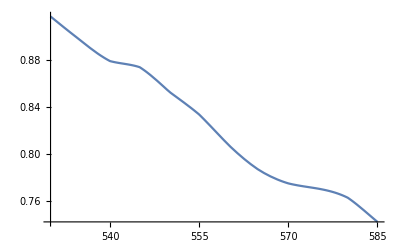

```mathematica
Plot[hola[x],{x,530,585}]
```

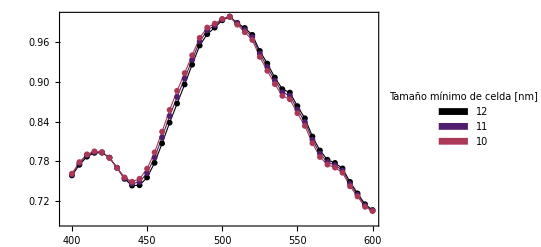

```mathematica
plotEriSano=ListPlot[dataQext[dataQabsEriSano[[#]],dataQscaEriSano[[#]]]&/@Range[1,3],PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12","11","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.2}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

### Propiedades ópticas

#### Importación y preparación de datos

```mathematica
dataEriSano=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_Cabs_Csca.csv"];
dataQabsEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,2]]/(Pi*3750^2)}];
dataQscaEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,3]]/(Pi*3750^2)}];

dataCabsEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,2]]}];
dataCscaEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,3]]}];
```

```mathematica
Plot[{dataQabsEriSanoFinal}]
```

#### Qext

```mathematica
ymin = Min[dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal][[All, 2]]];
ymax = Max[dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal][[All, 2]]];
```

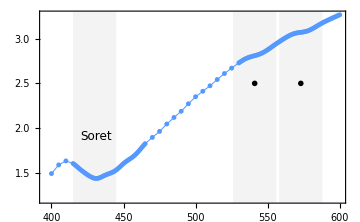

```mathematica
qExt30=ListPlot[{dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal]},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.2,Automatic}},
                      PlotStyle -> Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                       Prolog -> {
                      {
                      FaceForm[Directive[LightGray, Opacity[0.3]]],  EdgeForm[Transparent], Rectangle[{415, 0}, {445, 3.5}],Rectangle[{526, 0}, {556, 3.5}],Rectangle[{558, 0}, {588, 3.5}] },
                      Text[Style["Soret", 12, FontFamily->"Latin Modern Roman 10"],  {431, 1.9}],Text[Style[MaTeX["\\beta"], Magnification->1.05, FontFamily->"Latin Modern Roman 10"],  {541, 2.5}],
                      Text[Style[Style[MaTeX["\\alpha"], Magnification->1.05, FontFamily->"Latin Modern Roman 10"]],  {573, 2.5}] },
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["Qext_EriSano.svg",qExt30]
```

Qext_EriSano.svg

```mathematica
MinimalBy[dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal],Last]
```

{{431,1.43507}}

#### lambda = 431 nm

```mathematica
dataEriSanoFF431=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_431.csv"];

dataThetaEriSano431=Drop[dataEriSanoFF431,1][[All,1]];
dataPhiEriSano431=Drop[dataEriSanoFF431,1][[All,2]];
dataRCSEriSano431=Drop[dataEriSanoFF431,1][[All,3]];

data431 = Transpose[{dataThetaEriSano431 *Pi/180, dataPhiEriSano431*Pi/180, dataRCSEriSano431}];
data431Linear = Transpose[{dataThetaEriSano431 *Pi/180, dataPhiEriSano431*Pi/180, 10^(dataRCSEriSano431/10)}];
fInterp431 = Interpolation[data431,InterpolationOrder->1];
fInterp431Linear = Interpolation[data431Linear,InterpolationOrder->1];
min431 = Min[dataRCSEriSano431];
max431 = Max[dataRCSEriSano431];
```

```mathematica
dataFF4310=Table[{th,fInterp431[Abs[If[th > Pi, th - 2 Pi, th]], 0]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF431Pi=Table[{th,fInterp431[Abs[If[th > Pi, th - 2 Pi, th]], Pi]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF431Pi2=Table[{th,fInterp431[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]/(4 Pi)}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF431PiDegree=Table[{th*180/Pi,fInterp431[th, Pi]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF431Pi2DegreeLinear=Table[{th*180/Pi,fInterp431Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF4310DegreeLinear=Table[{th*180/Pi,fInterp431Linear[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

```mathematica
dataFF4310Theta=Table[{ph,fInterp431[0,Abs[If[ph > Pi, ph - 2 Pi, ph]]]/(4 Pi)}, {ph, 0, 2 Pi,Pi/100}];
dataFF431PiTheta=Table[{ph,fInterp431[Pi,Abs[If[ph > Pi, ph - 2 Pi, ph]]]/(4 Pi)}, {ph, 0,  2 Pi,Pi/100}];
dataFF431Pi2Theta=Table[{ph,fInterp431[Pi/2,Abs[If[ph > Pi, ph - 2 Pi, ph]]]/(4 Pi)}, {ph, 0,  2 Pi,Pi/100}];
```

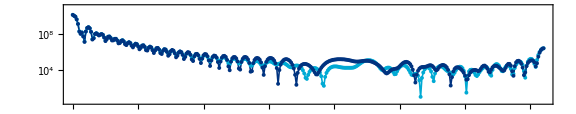

```mathematica
linearplot431FF=ListPlot[{dataFF4310DegreeLinear,dataFF431Pi2DegreeLinear},PlotMarkers->{"●",4},
                      Joined->True,
                      ScalingFunctions->"Log",
                      PlotRange->{{Automatic,Automatic},{10^(0.5),10^(11)}},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1]&/@{MaTeX["\\varphi=0^{\\circ}"],MaTeX["\\varphi=90^{\\circ}"]},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    
                                    Spacings->0.05],{0.8,0.8}],
                      PlotStyle -> {Directive[colorsCHCM[[1]], Thickness[0.002]],Directive[colorsCHCM[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{nm}^2] "],Magnification->1.05],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.05],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Large,
                      AspectRatio->2/10,
                      FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.25],
                      Evaluate[Sequence @@ plotStyling]]
```

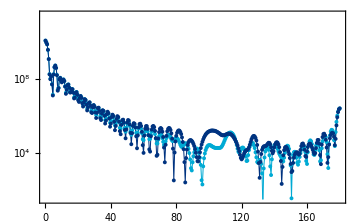

```mathematica
linearplot431FFV2=ListPlot[{dataFF4310DegreeLinear,dataFF431Pi2DegreeLinear},PlotMarkers->{"●",4},
                      Joined->True,
                      ScalingFunctions->"Log",
                      PlotRange->{{Automatic,Automatic},{10^(1.5),10^(11.5)}},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.35]&/@{MaTeX["\\varphi=0^{\\circ}"],MaTeX["\\varphi=90^{\\circ}"]},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    
                                    Spacings->0.05],{0.8,0.8}],
                      PlotStyle -> {Directive[colorsCHCM[[1]], Thickness[0.002]],Directive[colorsCHCM[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["linearplot431FF_EriSanoV2.svg",linearplot431FFV2]
```

linearplot431FF_EriSanoV2.svg

```mathematica
Export["linearplot431FF_EriSano.svg",linearplot431FF]
```

linearplot431FF_EriSano.svg

```mathematica
polarplot431FF = ListPolarPlot[
 {dataFF4310Theta, dataFF431PiTheta,dataFF431Pi2Theta},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 20, 40, 60, 80, 100}
 },

 PlotLegends -> Placed[
   {
    Style[MaTeX["\\varphi=0^{\\circ}"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=90^{\\circ}"], Magnification -> 1.7]
   },
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-180,0},{-180,120}}],

 (* ticks *)
   Table[   Line[{     {-183,r},     { -180,r}   }],
   {r,0,120,20}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-181.5,r},{ -180,r}}], {r,0,120,5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-205,r} ], {r,0,120,20}]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ colorsCHCM),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 150
]
```

-Graphics-

```mathematica
polarplot431FF = ListPolarPlot[
 {dataFF4310, dataFF431Pi2},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 2, 4, 6, 8, 10}
 },

  
 PlotLegends -> Placed[SwatchLegend[
   {
    Style[MaTeX["\\varphi=0^{\\circ}"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=90^{\\circ}"], Magnification -> 1.7]
   }],
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-15.0,0},{-15.0,10}}],

 (* ticks *)
   Table[   Line[{     {-15.3,r},     { -15.0,r}   }],
   {r,0,10,2}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-15.15,r},{ -15,r}}], {r,0,10,0.5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-16.5,r} ], {r,0,10,2}],
     Text[Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{dB}] "], Magnification->1.8],  {-16,12.0} ]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {bluelight30,bluedark30}),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 12
]
```

-Graphics-

```mathematica
Export["polarplot431FF_EriSano.svg",polarplot431FF]
```

polarplot431FF_EriSano.svg

```mathematica
Export["linearplot431FF_EriSano.svg",linearplot431FF]
```

polarplot431FF_EriSano.svg

linearplot431FF_EriSano.svg

```mathematica
data = Flatten[Table[{fInterp440[th, ph], th, ph}, {th, 0, Pi, Pi/100}, {ph, 0, 2 Pi, 2 Pi/100}], 1];
mapping =  CoordinateTransformData["Spherical" -> "Cartesian", "Mapping"];
ListPointPlot3D[mapping /@ data, BoxRatios -> Automatic]
```

InterpolatingFunction::dmval: Input value {0,2 π} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {π/100,2 π} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {π/50,2 π} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
cf431 = ColorMapSuite["lapaz"];
```

```mathematica
plotEriSano431axes=SphericalPlot3D[
 fInterp431[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
 PlotPoints -> 100,

 ColorFunction -> Function[{x, y, z, th, ph},
   cf431[
     Rescale[
       fInterp431[th, ph],
       {min431, max431}
     ]
   ]
 ],
 ColorFunctionScaling -> False,

 PlotStyle -> Opacity[1],
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 Mesh -> False,
 Exclusions -> None,

PlotLegends -> BarLegend[
 {cf431, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,\\,\\, "],Magnification->1.4]
],
 LabelStyle -> {
   Black,
   FontFamily -> "Latin Modern Roman 10",
   FontSize -> 18
 },
  ViewPoint -> {1, 1, 0}, 
  ViewVertical -> {0, -1, 0}
]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
plotEriSano431noaxes0=SphericalPlot3D[fInterp431[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
  ColorFunction -> Function[{x, y, z, th, ph},
   cf431[
     Rescale[
       fInterp431[th, ph],
       {min431, max431}
     ]
   ]
 ],
 
 ColorFunctionScaling -> False,
 
 PlotPoints -> 100,
 Boxed -> False,
 Axes -> False,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 
PlotLegends -> Placed[BarLegend[
 {cf431, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,\\,\\, "],Magnification->1.6]
],Top],
   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->20},
   ViewPoint -> {1, 1, 0}, 
  ViewVertical -> {0, -1, 0}
 ];

planeX=ParametricPlot3D[{0,y,z},{y,-100,100},{z,-100,120},PlotStyle->Directive[colorsCHCM[[2]],Opacity[0.35]],Mesh->None];

planeY=ParametricPlot3D[{x,0,z},{x,-100,100},{z,-100,120},PlotStyle->Directive[RGBColor[44/255,160/255,90/255],Specularity[100],Opacity[0.2]],Mesh->None];

plotEriSano431noaxes=Show[plotEriSano431noaxes0,planeX,planeY,PlotRange->All,Lighting->"Neutral"]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
colorsCHCM[[1]]
```

RGBColor[0, Rational[2, 3], Rational[212, 255]]

```mathematica
Export["FFdistribution431axes_EriSano.svg",plotEriSano431axes]
```

FFdistribution431axes_EriSano.svg

```mathematica
Export["FFdistribution431_EriSano.svg",plotEriSano431noaxes]
```

FFdistribution431_EriSano.svg

```mathematica
Export["grafica_editable.svg", graficaFinal, ]
```

#### lambda = 541 nm

```mathematica
dataEriSanoFF541=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_541.csv"];

dataThetaEriSano541=Drop[dataEriSanoFF541,1][[All,1]];
dataPhiEriSano541=Drop[dataEriSanoFF541,1][[All,2]];
dataRCSEriSano541=Drop[dataEriSanoFF541,1][[All,3]];

data541 = Transpose[{dataThetaEriSano541 *Pi/180, dataPhiEriSano541*Pi/180, dataRCSEriSano541}];
data541Linear = Transpose[{dataThetaEriSano541 *Pi/180, dataPhiEriSano541*Pi/180, 10^(dataRCSEriSano541/10)}];
fInterp541 = Interpolation[data541,InterpolationOrder->1];
fInterp541Linear = Interpolation[data541Linear,InterpolationOrder->1];
min541 = Min[dataRCSEriSano541];
max541 = Max[dataRCSEriSano541];
```

```mathematica
dataFF5410=Table[{th,fInterp541[Abs[If[th > Pi, th - 2 Pi, th]], 0]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF541Pi=Table[{th,fInterp541[Abs[If[th > Pi, th - 2 Pi, th]], Pi]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF541Pi2=Table[{th,fInterp541[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]/(4 Pi)}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF541PiDegree=Table[{th*180/Pi,fInterp541[th, Pi]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF541Pi2DegreeLinear=Table[{th*180/Pi,fInterp541Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF5410DegreeLinear=Table[{th*180/Pi,fInterp541Linear[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

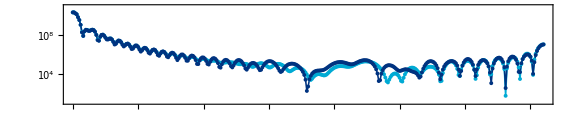

```mathematica
linearplot541FF=ListPlot[{dataFF5410DegreeLinear,dataFF541Pi2DegreeLinear},PlotMarkers->{"●",4},
                      Joined->True,
                      ScalingFunctions->"Log",
                      PlotRange->{{Automatic,Automatic},{10^(1),10^(11
                      )}},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1]&/@{MaTeX["\\varphi=0^{\\circ}"],MaTeX["\\varphi=90^{\\circ}"]},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    
                                    Spacings->0.05],{0.8,0.8}],
                      PlotStyle -> {Directive[colorsCHCM[[1]], Thickness[0.002]],Directive[colorsCHCM[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{nm}^2] "],Magnification->1.05],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.05],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Large,
                      AspectRatio->2/10,
                      FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.25],
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["linearplot541FF_EriSano.svg",linearplot541FF]
```

linearplot541FF_EriSano.svg

```mathematica
polarplot541FF = ListPolarPlot[
 {dataFF5410, dataFF541Pi2},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 2, 4, 6, 8, 10}
 },

  
 PlotLegends -> Placed[SwatchLegend[
   {
    Style[MaTeX["\\varphi=0^{\\circ}"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=90^{\\circ}"], Magnification -> 1.7]
   }],
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-15.0,0},{-15.0,10}}],

 (* ticks *)
   Table[   Line[{     {-15.3,r},     { -15.0,r}   }],
   {r,0,10,2}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-15.15,r},{ -15,r}}], {r,0,10,0.5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-16.5,r} ], {r,0,10,2}],
     Text[Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{dB}] "], Magnification->1.8],  {-16,12.0} ]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {bluelight30,bluedark30}),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 12
]
```

-Graphics-

```mathematica
Export["polarplot541FF_EriSano.svg",polarplot541FF]
```

polarplot541FF_EriSano.svg

```mathematica
N[331 Pi/360]*180/Pi
N[389 Pi/360]*180/Pi
```

165.5

194.5

```mathematica
MinimalBy[dataFF5410,Last]
```

{{(331 π)/360,2.21225},{(389 π)/360,2.21225}}

```mathematica
cf541 = ColorMapSuite["oslo"];
```

```mathematica
plotEriSano541axes=SphericalPlot3D[
 fInterp541[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
 PlotPoints -> 100,

 ColorFunction -> Function[{x, y, z, th, ph},
   cf431[
     Rescale[
       fInterp541[th, ph],
       {min541, max541}
     ]
   ]
 ],
 ColorFunctionScaling -> False,

 PlotStyle -> Opacity[1],
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 Mesh -> False,
 Exclusions -> None,

PlotLegends -> BarLegend[
 {cf431, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,\\,\\, "],Magnification->1.4]
],
 LabelStyle -> {
   Black,
   FontFamily -> "Latin Modern Roman 10",
   FontSize -> 18
 },
  ViewPoint -> {1, 12, 0}, 
  ViewVertical -> {0, -1, 0}
]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
plotEriSano541noaxes0=SphericalPlot3D[fInterp541[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
  ColorFunction -> Function[{x, y, z, th, ph},
   cf431[
     Rescale[
       fInterp541[th, ph],
       {min541, max541}
     ]
   ]
 ],
 
 ColorFunctionScaling -> False,
 
 PlotPoints -> 100,
 Boxed -> False,
 Axes -> False,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 
PlotLegends -> Placed[BarLegend[
 {cf431, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["(\\text{d}C_{\\text{sca}}/\\text{d}\\Omega)/(\\text{d}C_{\\text{sca}}/\\text{d}\\Omega)_{\\text{max}}\\,\\,\\, "],
 Magnification->1.6]
],Top],
   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->20},
   ViewPoint -> {1, 1, 0}, 
  ViewVertical -> {0, -1, 0}
 ];

planeX=ParametricPlot3D[{0,y,z},{y,-100,100},{z,-100,120},PlotStyle->Directive[colorsCHCM[[2]],Opacity[0.35]],Mesh->None];

planeY=ParametricPlot3D[{x,0,z},{x,-100,100},{z,-100,120},PlotStyle->Directive[RGBColor[44/255,160/255,90/255],Specularity[100],Opacity[0.2]],Mesh->None];

plotEriSano541noaxes=Show[plotEriSano541noaxes0,planeX,planeY,PlotRange->All]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Export["FFdistribution541axes_EriSano.svg",plotEriSano541axes]
```

FFdistribution541axes_EriSano.svg

```mathematica
Export["FFdistribution541_EriSano.svg",plotEriSano541noaxes]
```

FFdistribution541_EriSano.svg

```mathematica
Export["grafica_editable.svg", graficaFinal, ]
```

#### lambda = 573 nm

```mathematica
dataEriSanoFF573=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_573.csv"];

dataThetaEriSano573=Drop[dataEriSanoFF573,1][[All,1]];
dataPhiEriSano573=Drop[dataEriSanoFF573,1][[All,2]];
dataRCSEriSano573=Drop[dataEriSanoFF573,1][[All,3]];

data573 = Transpose[{dataThetaEriSano573 *Pi/180, dataPhiEriSano573*Pi/180, dataRCSEriSano573}];
data573Linear = Transpose[{dataThetaEriSano541 *Pi/180, dataPhiEriSano573*Pi/180, 10^(dataRCSEriSano573/10)}];
fInterp573 = Interpolation[data573,InterpolationOrder->1];
fInterp573Linear = Interpolation[data573Linear,InterpolationOrder->1];
min573 = Min[dataRCSEriSano573];
max573 = Max[dataRCSEriSano573];
```

```mathematica
dataFF5730=Table[{th,fInterp573[Abs[If[th > Pi, th - 2 Pi, th]], 0]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF573Pi=Table[{th,fInterp573[Abs[If[th > Pi, th - 2 Pi, th]], Pi]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF573Pi2=Table[{th,fInterp573[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]/(4 Pi)}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF573PiDegree=Table[{th*180/Pi,fInterp573[th, Pi]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF573Pi2DegreeLinear=Table[{th*180/Pi,fInterp573Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF5730DegreeLinear=Table[{th*180/Pi,fInterp573Linear[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

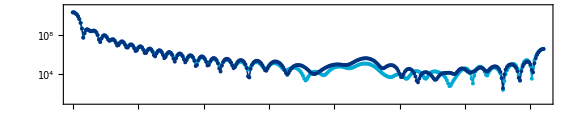

```mathematica
linearplot573FF=ListPlot[{dataFF5730DegreeLinear,dataFF573Pi2DegreeLinear},PlotMarkers->{"●",4},
                      Joined->True,
                      ScalingFunctions->"Log",
                      PlotRange->{{Automatic,Automatic},{10^(1),10^(11)}},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1]&/@{MaTeX["\\varphi=0^{\\circ}"],MaTeX["\\varphi=90^{\\circ}"]},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    
                                    Spacings->0.05],{0.8,0.8}],
                      PlotStyle -> {Directive[colorsCHCM[[1]], Thickness[0.002]],Directive[colorsCHCM[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{nm}^2] "],Magnification->1.05],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.05],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Large,
                      AspectRatio->2/10,
                      FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.25],
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["linearplot573FF_EriSano.svg",linearplot573FF]
```

linearplot573FF_EriSano.svg

```mathematica
polarplot573FF = ListPolarPlot[
 {dataFF5730, dataFF573Pi2},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 2, 4, 6, 8, 10}
 },

  
 PlotLegends -> Placed[SwatchLegend[
   {
    Style[MaTeX["\\varphi=0^{\\circ}"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=90^{\\circ}"], Magnification -> 1.7]
   }],
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-15.0,0},{-15.0,10}}],

 (* ticks *)
   Table[   Line[{     {-15.3,r},     { -15.0,r}   }],
   {r,0,10,2}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-15.15,r},{ -15,r}}], {r,0,10,0.5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-16.5,r} ], {r,0,10,2}],
     Text[Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{dB}] "], Magnification->1.8],  {-16,12.0} ]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {bluelight30,bluedark30}),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 12
]
```

-Graphics-

```mathematica
Export["polarplot573FF_EriSano.svg",polarplot573FF]
```

polarplot573FF_EriSano.svg

```mathematica
cf541 = ColorMapSuite["oslo"];
```

```mathematica
plotEriSano573axes=SphericalPlot3D[
 fInterp573[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
 PlotPoints -> 100,

 ColorFunction -> Function[{x, y, z, th, ph},
   cf431[
     Rescale[
       fInterp573[th, ph],
       {min541, max541}
     ]
   ]
 ],
 ColorFunctionScaling -> False,

 PlotStyle -> Opacity[1],
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 Mesh -> False,
 Exclusions -> None,

PlotLegends -> BarLegend[
 {cf431, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,\\,\\, "],Magnification->1.4]
],
 LabelStyle -> {
   Black,
   FontFamily -> "Latin Modern Roman 10",
   FontSize -> 18
 },
  ViewPoint -> {1, 12, 0}, 
  ViewVertical -> {0, -1, 0}
]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
plotEriSano573noaxes0=SphericalPlot3D[fInterp573[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
  ColorFunction -> Function[{x, y, z, th, ph},
   cf431[
     Rescale[
       fInterp573[th, ph],
       {min541, max541}
     ]
   ]
 ],
 
 ColorFunctionScaling -> False,
 
 PlotPoints -> 100,
 Boxed -> False,
 Axes -> False,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 
PlotLegends -> Placed[BarLegend[
 {cf431, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["(\\text{d}C_{\\text{sca}}/\\text{d}\\Omega)/(\\text{d}C_{\\text{sca}}/\\text{d}\\Omega)_{\\text{max}}\\,\\,\\, "],
 Magnification->1.6]
],Top],
   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->20},
   ViewPoint -> {1, 1, 0}, 
  ViewVertical -> {0, -1, 0}
 ];

planeX=ParametricPlot3D[{0,y,z},{y,-100,100},{z,-100,120},PlotStyle->Directive[colorsCHCM[[2]],Opacity[0.35]],Mesh->None];

planeY=ParametricPlot3D[{x,0,z},{x,-100,100},{z,-100,120},PlotStyle->Directive[RGBColor[44/255,160/255,90/255],Specularity[100],Opacity[0.2]],Mesh->None];

plotEriSano573noaxes=Show[plotEriSano573noaxes0,planeX,planeY,PlotRange->All]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Export["FFdistribution573axes_EriSano.svg",plotEriSano573axes]
```

FFdistribution573axes_EriSano.svg

```mathematica
Export["FFdistribution573_EriSano.svg",plotEriSano573noaxes]
```

FFdistribution573_EriSano.svg

```mathematica
Export["grafica_editable.svg", graficaFinal, ]
```

### Cálculo de propiedades

#### Factor de anisotropía

```mathematica
fInterp431Linear = Interpolation[data431Linear];
CscaInt431 = NIntegrate[(fInterp431Linear[th, phi]/(4 Pi))* Sin[th], {th, 0, Pi}, {phi, 0, 2 Pi}];

g431 = NIntegrate[ (fInterp431Linear[th, phi]/(4 Pi))* Cos[th]*Sin[th],{th, 0, Pi},{phi, 0, 2 Pi}]/CscaInt431
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.98933×10^7 and 12206. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.83836×10^7 and 9079.74 for the integral and error estimates.

0.96974

```mathematica
CscaInt431
```

4.98933×10^7

```mathematica
fInterp541Linear = Interpolation[data541Linear];
CscaInt541 = NIntegrate[(fInterp541Linear[th, phi]/(4 Pi))* Sin[th], {th, 0, Pi}, {phi, 0, 2 Pi}];

g541 = NIntegrate[ (fInterp541Linear[th, phi]/(4 Pi))* Cos[th]*Sin[th],{th, 0, Pi},{phi, 0, 2 Pi}]/CscaInt541
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.1913×10^8 and 8251.44 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.16941×10^8 and 6356.99 for the integral and error estimates.

0.981629

```mathematica
fInterp573Linear = Interpolation[data573Linear];
CscaInt573 = NIntegrate[(fInterp573Linear[th, phi]/(4 Pi))* Sin[th], {th, 0, Pi}, {phi, 0, 2 Pi}];

g573= NIntegrate[ (fInterp573Linear[th, phi]/(4 Pi))* Cos[th]*Sin[th],{th, 0, Pi},{phi, 0, 2 Pi}]/CscaInt573
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2796×10^8 and 7052.81 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.26209×10^8 and 5366.65 for the integral and error estimates.

0.986311

#### Correlaciones

```mathematica
fInterp431Linear = Interpolation[data431Linear,InterpolationOrder->1];

dataFF431Pi2DegreeLinearFront=Table[fInterp431Linear[th, Pi/2]/(4 Pi), {th, 0,  Pi/3,  Pi/60}];
dataFF431Pi2DegreeLinearLat=Table[fInterp431Linear[th, Pi/2]/(4 Pi), {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF431Pi2DegreeLinearRetro=Table[fInterp431Linear[th, Pi/2]/(4 Pi), {th, 2 Pi/3,  Pi,  Pi/60}];

dataFF4310DegreeLinearFront=Table[fInterp431Linear[th, 0]/(4 Pi), {th, 0,  Pi/3,  Pi/60}];
dataFF4310DegreeLinearLat=Table[fInterp431Linear[th, 0]/(4 Pi), {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF4310DegreeLinearRetro=Table[fInterp431Linear[th, 0]/(4 Pi), {th, 2 Pi/3,  Pi,  Pi/60}];
```

```mathematica
N[dataFF431Pi2DegreeLinear]
```

{{0.,1.26122×10^10},{0.5,1.00182×10^10},{1.,7.95775×10^9},{1.5,3.98832×10^9},{2.,1.26122×10^9},{2.5,1.86548×10^8},{3.,1.02516×10^8},{3.5,1.44807×10^8},{4.,5.3801×10^7},{4.5,1.35142×10^7},{5.,1.86548×10^8},{5.5,4.57921×10^8},{6.,5.63365×10^8},{6.5,4.17629×10^8},{7.,1.70134×10^8},{7.5,2.45918×10^7},{8.,3.39461×10^7},{8.5,1.00182×10^8},{9.,1.20445×10^8},{9.5,9.13672×10^7},{10.,6.93091×10^7},{10.5,8.33278×10^7},{11.,9.79017×10^7},{11.5,8.14311×10^7},{12.,4.08122×10^7},{12.5,1.66261×10^7},{13.,2.69644×10^7},{13.5,4.90671×10^7},{14.,5.25763×10^7},{14.5,3.5546×10^7},{15.,1.9534×10^7},{15.5,1.9989×10^7},{16.,2.88928×10^7},{16.5,2.95658×10^7},{17.,1.90893×10^7},{17.5,9.34954×10^6},{18.,1.02516×10^7},{18.5,1.74097×10^7},{19.,2.04546×10^7},{19.5,1.4818×10^7},{20.,7.4266×10^6},{20.5,6.03657×10^6},{21.,1.00182×10^7},{21.5,1.26122×10^7},{22.,1.00182×10^7},{22.5,5.13795×10^6},{23.,3.39461×10^6},{23.5,5.76488×10^6},{24.,8.52688×10^6},{24.5,7.59959×10^6},{25.,4.27356×10^6},{25.5,2.0931×10^6},{26.,3.02545×10^6},{26.5,5.25763×10^6},{27.,5.76488×10^6},{27.5,3.80882×10^6},{28.,1.66261×10^6},{28.5,1.51632×10^6},{29.,3.02545×10^6},{29.5,4.08122×10^6},{30.,3.31734×10^6},{30.5,1.62476×10^6},{31.,814311.},{31.5,1.55164×10^6},{32.,2.75924×10^6},{32.5,2.95658×10^6},{33.,1.9534×10^6},{33.5,795775.},{34.,632106.},{34.5,1.41511×10^6},{35.,2.14186×10^6},{35.5,1.9534×10^6},{36.,1.07347×10^6},{36.5,408122.},{37.,589916.},{37.5,1.32066×10^6},{38.,1.78152×10^6},{38.5,1.4818×10^6},{39.,759959.},{39.5,275924.},{40.,408122.},{40.5,913672.},{41.,1.23251×10^6},{41.5,1.02516×10^6},{42.,502100.},{42.5,178152.},{43.,302545.},{43.5,725755.},{44.,1.02516×10^6},{44.5,913672.},{45.,513795.},{45.5,158778.},{46.,107347.},{46.5,347368.},{47.,617718.},{47.5,661897.},{48.,457921.},{48.5,182301.},{49.,64683.},{49.5,195340.},{50.,457921.},{50.5,632106.},{51.,589916.},{51.5,363739.},{52.,126122.},{52.5,30959.2},{53.,123251.},{53.5,302545.},{54.,427356.},{54.5,398832.},{55.,251646.},{55.5,83327.8},{56.,18654.8},{56.5,93495.4},{57.,251646.},{57.5,380882.},{58.,398832.},{58.5,302545.},{59.,144807.},{59.5,27592.4},{60.,10490.4},{60.5,91367.2},{61.,214186.},{61.5,295658.},{62.,295658.},{62.5,209310.},{63.,95673.2},{63.5,16247.6},{64.,12325.1},{64.5,83327.8},{65.,190893.},{65.5,282352.},{66.,302545.},{66.5,257508.},{67.,162476.},{67.5,66189.7},{68.,7257.55},{68.5,8332.78},{69.,63210.6},{69.5,141511.},{70.,209310.},{70.5,234850.},{71.,209310.},{71.5,148180.},{72.,75995.9},{72.5,20454.6},{73.,3241.83},{73.5,28892.8},{74.,87255.},{74.5,155164.},{75.,209310.},{75.5,234850.},{76.,224280.},{76.5,182301.},{77.,120445.},{77.5,61771.8},{78.,17815.2},{78.5,339.461},{79.,10984.7},{79.5,43731.1},{80.,87255.},{80.5,129060.},{81.,158778.},{81.5,174097.},{82.,166261.},{82.5,141511.},{83.,109847.},{83.5,72575.5},{84.,40812.2},{84.5,16626.1},{85.,3317.34},{85.5,263.506},{86.,5505.42},{86.5,15877.8},{87.,28235.2},{87.5,39883.2},{88.,47950.2},{88.5,51379.5},{89.,51379.5},{89.5,46858.7},{90.,40812.2},{90.5,32418.3},{91.,24591.8},{91.5,17013.4},{92.,10734.7},{92.5,6177.18},{93.,3722.12},{93.5,3637.39},{94.,6177.18},{94.5,11240.6},{95.,19089.3},{95.5,29565.8},{96.,41762.9},{96.5,56336.5},{97.,72575.5},{97.5,87255.},{98.,104904.},{98.5,117704.},{99.,132066.},{99.5,144807.},{100.,151632.},{100.5,158778.},{101.,166261.},{101.5,170134.},{102.,170134.},{102.5,170134.},{103.,166261.},{103.5,166261.},{104.,158778.},{104.5,151632.},{105.,144807.},{105.5,135142.},{106.,126122.},{106.5,117704.},{107.,107347.},{107.5,100182.},{108.,95673.2},{108.5,93495.4},{109.,93495.4},{109.5,95673.2},{110.,100182.},{110.5,104904.},{111.,109847.},{111.5,115024.},{112.,115024.},{112.5,115024.},{113.,112406.},{113.5,104904.},{114.,97901.7},{114.5,87255.},{115.,75995.9},{115.5,64683.},{116.,53801.},{116.5,43731.1},{117.,34736.8},{117.5,26350.6},{118.,18654.8},{118.5,12906.},{119.,8332.78},{119.5,5633.65},{120.,4685.87},{120.5,5505.42},{121.,7257.55},{121.5,9790.17},{122.,12044.5},{122.5,13829.},{123.,14480.7},{123.5,15516.4},{124.,17013.4},{124.5,20931.},{125.,28892.8},{125.5,40812.2},{126.,56336.5},{126.5,70923.5},{127.,83327.8},{127.5,87255.},{128.,81431.1},{128.5,67731.4},{129.,49067.1},{129.5,28235.2},{130.,12325.1},{130.5,2956.58},{131.,468.587},{131.5,3394.61},{132.,9136.72},{132.5,15516.4},{133.,20454.6},{133.5,23485.},{134.,24032.},{134.5,24591.8},{135.,25750.8},{135.5,28892.8},{136.,33173.4},{136.5,37221.2},{137.,36373.9},{137.5,30254.5},{138.,21418.6},{138.5,13514.2},{139.,10018.2},{139.5,12906.},{140.,20931.},{140.5,30254.5},{141.,37221.2},{141.5,39883.2},{142.,37221.2},{142.5,30254.5},{143.,21418.6},{143.5,11502.4},{144.,3808.82},{144.5,219.175},{145.,1823.01},{145.5,7776.61},{146.,14818.},{146.5,20454.6},{147.,22428.},{147.5,20931.},{148.,17013.4},{148.5,12906.},{149.,8928.74},{149.5,5505.42},{150.,2635.06},{150.5,956.732},{151.,1098.47},{151.5,3025.45},{152.,5764.88},{152.5,8332.78},{153.,10251.6},{153.5,11240.6},{154.,11240.6},{154.5,9790.17},{155.,8332.78},{155.5,9567.32},{156.,15163.2},{156.5,24591.8},{157.,32418.3},{157.5,33946.1},{158.,26350.6},{158.5,15516.4},{159.,7092.35},{159.5,6321.06},{160.,12612.2},{160.5,21917.5},{161.,29565.8},{161.5,33173.4},{162.,32418.3},{162.5,26964.4},{163.,20931.},{163.5,15516.4},{164.,11502.4},{164.5,9136.72},{165.,10251.6},{165.5,19089.3},{166.,36373.9},{166.5,52576.3},{167.,52576.3},{167.5,33173.4},{168.,7957.75},{168.5,2575.08},{169.,29565.8},{169.5,75995.9},{170.,109847.},{170.5,115024.},{171.,91367.2},{171.5,53801.},{172.,20454.6},{172.5,3025.45},{173.,6177.18},{173.5,29565.8},{174.,64683.},{174.5,97901.7},{175.,120445.},{175.5,129060.},{176.,117704.},{176.5,77766.1},{177.,27592.4},{177.5,60365.7},{178.,324183.},{178.5,892874.},{179.,1.70134×10^6},{179.5,2.4032×10^6},{180.,2.69644×10^6}}

```mathematica
lm=LinearModelFit[
 Transpose[{dataFF431Pi2DegreeLinearFront,dataFF4310DegreeLinearFront}],
 x,
 x
]
```

FittedModel[760226.+0.999943 x]

```mathematica
lm["RSquared"]
```

1.

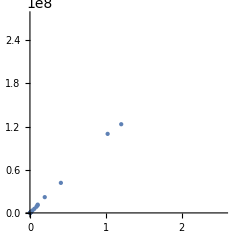

```mathematica
ListPlot[Transpose[{dataFF431Pi2DegreeLinearFront,dataFF4310DegreeLinearFront}],AspectRatio->1]
```

```mathematica
r = Total[(dataFF431Pi2DegreeLinearFront - Mean[dataFF431Pi2DegreeLinearFront]) (dataFF4310DegreeLinearFront - Mean[dataFF4310DegreeLinearFront])]/
    Sqrt[Total[(dataFF431Pi2DegreeLinearFront - Mean[dataFF431Pi2DegreeLinearFront])^2] Total[(dataFF4310DegreeLinearFront - Mean[dataFF4310DegreeLinearFront])^2]]
```

1.

```mathematica
N[Correlation[dataFF4310DegreeLinearFront,dataFF431Pi2DegreeLinearFront],20]
Correlation[dataFF4310DegreeLinearLat,dataFF431Pi2DegreeLinearLat]
Correlation[dataFF4310DegreeLinearRetro,dataFF431Pi2DegreeLinearRetro]
```

1.

0.668136

0.999697

```mathematica
fInterp541Linear = Interpolation[data541Linear,InterpolationOrder->1];

dataFF541Pi2DegreeLinearFront=Table[{fInterp541Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi/3,  Pi/60}];
dataFF541Pi2DegreeLinearLat=Table[{fInterp541Linear[th, Pi/2]/(4 Pi)}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF541Pi2DegreeLinearRetro=Table[{fInterp541Linear[th, Pi/2]/(4 Pi)}, {th, 2 Pi/3,  Pi,  Pi/60}];

dataFF5410DegreeLinearFront=Table[{fInterp541Linear[th, 0]/(4 Pi)}, {th, 0,  Pi/3,  Pi/60}];
dataFF5410DegreeLinearLat=Table[{fInterp541Linear[th, 0]/(4 Pi)}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF5410DegreeLinearRetro=Table[{fInterp541Linear[th, 0]/(4 Pi)}, {th, 2 Pi/3,  Pi,  Pi/60}];
```

```mathematica
Correlation[dataFF5410DegreeLinearFront,dataFF541Pi2DegreeLinearFront]
Correlation[dataFF5410DegreeLinearLat,dataFF541Pi2DegreeLinearLat]
Correlation[dataFF5410DegreeLinearRetro,dataFF541Pi2DegreeLinearRetro]
```

{{1.}}

{{0.499152}}

{{0.999226}}

```mathematica
fInterp573Linear = Interpolation[data573Linear,InterpolationOrder->1];

dataFF573Pi2DegreeLinearFront=Table[{fInterp573Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi/3,  Pi/60}];
dataFF573Pi2DegreeLinearLat=Table[{fInterp573Linear[th, Pi/2]/(4 Pi)}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF573Pi2DegreeLinearRetro=Table[{fInterp573Linear[th, Pi/2]/(4 Pi)}, {th, 2 Pi/3,  Pi,  Pi/60}];

dataFF5730DegreeLinearFront=Table[{fInterp573Linear[th, 0]/(4 Pi)}, {th, 0,  Pi/3,  Pi/60}];
dataFF5730DegreeLinearLat=Table[{fInterp573Linear[th, 0]/(4 Pi)}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF5730DegreeLinearRetro=Table[{fInterp573Linear[th, 0]/(4 Pi)}, {th, 2 Pi/3,  Pi,  Pi/60}];
```

```mathematica
Correlation[dataFF5730DegreeLinearFront,dataFF573Pi2DegreeLinearFront]
Correlation[dataFF5730DegreeLinearLat,dataFF573Pi2DegreeLinearLat]
Correlation[dataFF5730DegreeLinearRetro,dataFF573Pi2DegreeLinearRetro]
```

{{1.}}

{{0.70656}}

{{0.997843}}

#### Contribuciones integradas

```mathematica
CscaInt431Front0 = NIntegrate[(fInterp431Linear[th, 0]/(4 Pi))* Sin[th], {th, 0, Pi/3}]
CscaInt431FrontPi2 = NIntegrate[(fInterp431Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, 0, Pi/3}]

CscaInt431FrontDif=100*Abs[CscaInt431Front0-CscaInt431FrontPi2]/CscaInt431Front0

CscaInt431Lat0 = NIntegrate[(fInterp431Linear[th, 0]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]
CscaInt431LatPi2 = NIntegrate[(fInterp431Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]

CscaInt431LatDif=100*Abs[CscaInt431Lat0-CscaInt431LatPi2]/CscaInt431Lat0

CscaInt431Retro0 = NIntegrate[(fInterp431Linear[th, 0]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]
CscaInt431RetroPi2 = NIntegrate[(fInterp431Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]

CscaInt431RetroDif=100*Abs[CscaInt431Retro0-CscaInt431RetroPi2]/CscaInt431Retro0
```

8.028×10^6

7.90145×10^6

1.57634

51736.5

95881.9

85.3274

8881.92

13114.1

47.6498

```mathematica
CscaInt431Front0/(Pi * 3750^2)
CscaInt431Lat0/(Pi * 3750^2)
CscaInt431Retro0/(Pi * 3750^2)

CscaInt431FrontPi2/(Pi * 3750^2)
CscaInt431LatPi2/(Pi * 3750^2)
CscaInt431RetroPi2/(Pi * 3750^2)
```

0.181717

0.00117107

0.000201046

0.178852

0.00217032

0.000296843

```mathematica
total0Eri=CscaInt431Front0+CscaInt431Lat0+CscaInt431Retro0;
CscaInt431Front0/total0Eri
CscaInt431Lat0/total0Eri
CscaInt431Retro0/total0Eri
```

0.992506

0.00639621

0.00109808

```mathematica
totalPi2Eri=CscaInt431FrontPi2+CscaInt431LatPi2+CscaInt431RetroPi2;
CscaInt431FrontPi2/totalPi2Eri
CscaInt431LatPi2/totalPi2Eri
CscaInt431RetroPi2/totalPi2Eri
```

0.986393

0.0119696

0.00163713

```mathematica
N[(Pi * 3750^2)]
```

4.41786×10^7

```mathematica
CscaInt541Front0 = NIntegrate[(fInterp541Linear[th, 0]/(4 Pi))* Sin[th], {th, 0, Pi/3}]
CscaInt541FrontPi2 = NIntegrate[(fInterp541Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, 0, Pi/3}]

CscaInt541FrontDif=100*Abs[CscaInt541Front0-CscaInt541FrontPi2]/CscaInt541Front0


CscaInt541Lat0 = NIntegrate[(fInterp541Linear[th, 0]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]
CscaInt541LatPi2 = NIntegrate[(fInterp541Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]

CscaInt541LatDif=100*Abs[CscaInt541Lat0-CscaInt541LatPi2]/CscaInt541Lat0


CscaInt541Retro0 = NIntegrate[(fInterp541Linear[th, 0]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]
CscaInt541RetroPi2 = NIntegrate[(fInterp541Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]

CscaInt541RetroDif=100*Abs[CscaInt541Retro0-CscaInt541RetroPi2]/CscaInt541Retro0
```

1.91037×10^7

1.89795×10^7

0.650345

66659.

92567.5

38.8671

47648.4

60836.2

27.6775

```mathematica
CscaInt541Front0/(Pi * 3750^2)
CscaInt541Lat0/(Pi * 3750^2)
CscaInt541Retro0/(Pi * 3750^2)

CscaInt541FrontPi2/(Pi * 3750^2)
CscaInt541LatPi2/(Pi * 3750^2)
CscaInt541RetroPi2/(Pi * 3750^2)
```

0.43242

0.00150885

0.00107854

0.429607

0.0020953

0.00137705

```mathematica
Abs[CscaInt541Front0/(Pi * 3750^2)-CscaInt541FrontPi2/(Pi * 3750^2)]
Abs[CscaInt541Lat0/(Pi * 3750^2)-CscaInt541LatPi2/(Pi * 3750^2)]
Abs[CscaInt541Retro0/(Pi * 3750^2)-CscaInt541RetroPi2/(Pi * 3750^2)]
```

0.00281222

0.000586446

0.000298512

```mathematica
CscaInt573Front0 = NIntegrate[(fInterp573Linear[th, 0]/(4 Pi))* Sin[th], {th, 0, Pi/3}]
CscaInt573FrontPi2 = NIntegrate[(fInterp573Linear[th,Pi/2]/(4 Pi))* Sin[th], {th, 0, Pi/3}]

CscaInt573FrontDif=100*Abs[CscaInt573Front0-CscaInt573FrontPi2]/CscaInt573Front0

CscaInt573Lat0 = NIntegrate[(fInterp573Linear[th, 0]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]
CscaInt573LatPi2 = NIntegrate[(fInterp573Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]

CscaInt573LatDif=100*Abs[CscaInt573Lat0-CscaInt573LatPi2]/CscaInt573Lat0


CscaInt573Retro0 = NIntegrate[(fInterp573Linear[th, 0]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]
CscaInt573RetroPi2 = NIntegrate[(fInterp573Linear[th,Pi/2]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]

CscaInt573RetroDif=100*Abs[CscaInt573Retro0-CscaInt573RetroPi2]/CscaInt573Retro0
```

2.05433×10^7

2.04389×10^7

0.508157

56327.8

111729.

98.3554

10872.

15076.5

38.6723

```mathematica
CscaInt573Front0/(Pi * 3750^2)
CscaInt573Lat0/(Pi * 3750^2)
CscaInt573Retro0/(Pi * 3750^2)

CscaInt573FrontPi2/(Pi * 3750^2)
CscaInt573LatPi2/(Pi * 3750^2)
CscaInt573RetroPi2/(Pi * 3750^2)
```

0.465005

0.001275

0.000246093

0.462642

0.00252903

0.000341262

## lambda = 431 nm

### Comparación con Papers

#### Skalak

```mathematica
dataSkalakCSTFF=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Skalak_CST_FF_2.csv"];

dataThetaEriSanoSkalak=Drop[dataSkalakCSTFF,1][[All,1]];
dataPhiEriSanoSkalak=Drop[dataSkalakCSTFF,1][[All,2]];
dataRCSEriSanoSkalak=Drop[dataSkalakCSTFF,1][[All,3]];

data632 = Transpose[{dataThetaEriSanoSkalak *Pi/180, dataPhiEriSanoSkalak*Pi/180, dataRCSEriSanoSkalak}];
data632Linear = Transpose[{dataThetaEriSanoSkalak *Pi/180, dataPhiEriSanoSkalak*Pi/180, 10^(dataRCSEriSanoSkalak/10)}];
fInterp632 = Interpolation[data632,InterpolationOrder->1];
fInterp632Linear = Interpolation[data632Linear,InterpolationOrder->1];
min632 = Min[dataRCSEriSanoSkalak];
max632 = Max[dataRCSEriSanoSkalak];
```

```mathematica
dataSkalakpaper=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Skalak_paper.csv"];
datapaperSkalak=Interpolation[Transpose[{dataSkalakpaper[[All,1]],dataSkalakpaper[[All,2]]*10^6}],InterpolationOrder->1];
datapaperplotSkalak=Table[{x,datapaperSkalak[x]},{x,0,180,0.05}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dataFF6320=Table[{th,fInterp632[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi,Pi/360}];
dataFF632Pi=Table[{th,fInterp632[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0,  2 Pi,Pi/360}];
dataFF632Pi2=Table[{th,fInterp632[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF632Pi2Degree=Table[{th*180/Pi,fInterp632[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF632Pi2DegreeLinear=Table[{th*180/Pi,fInterp632Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF6320DegreeLinear=Table[{th*180/Pi,fInterp632Linear[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

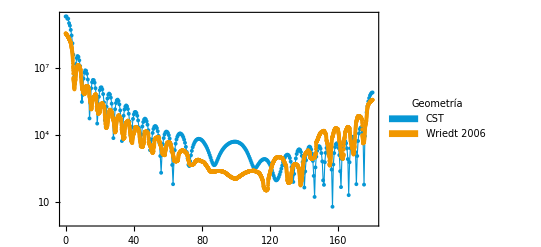

```mathematica
comparacionpaper=ListPlot[{dataFF632Pi2DegreeLinear,datapaperplotSkalak},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], 
                      Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]
                                                       &/@{"CST","Wriedt 2006","Tsin"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Evaluate[Sequence @@ plotStyling]]
```

#### Tsinopoulos

```mathematica
dataDSCSpaper=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\DSCS_paper.csv"];
datapaper=Interpolation[Transpose[{dataDSCSpaper[[All,1]],dataDSCSpaper[[All,2]]*10^6}],InterpolationOrder->1];
datapaperplot=Table[{x,datapaper[x]},{x,0,180,0.05}];


dataDSCSpaper0=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\DSCS_paper_theta0.csv"];
datapaper0=Interpolation[Transpose[{dataDSCSpaper0[[All,1]],dataDSCSpaper0[[All,2]]*10^6}],InterpolationOrder->1];
datapaperplot0=Table[{x,datapaper0[x]},{x,0,180,0.05}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

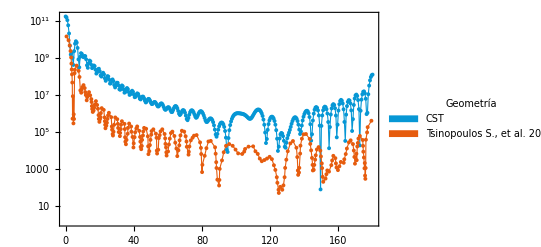

```mathematica
comparacionpaper=ListPlot[{dataFF4400DegreeLinear,datapaper},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[1]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","Tsinopoulos S., et al. 2002"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["paperComp.svg",comparacionpaper]
```

paperComp.svg

```mathematica
dataTsiCSTFF=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Tsinopoulos_CST_FF_2.csv"];

dataThetaEriSanoTsi=Drop[dataTsiCSTFF,1][[All,1]];
dataPhiEriSanoTsi=Drop[dataTsiCSTFF,1][[All,2]];
dataRCSEriSanoTsi=Drop[dataTsiCSTFF,1][[All,3]];

data632Tsi = Transpose[{dataThetaEriSanoTsi *Pi/180, dataPhiEriSanoTsi*Pi/180, dataRCSEriSanoTsi}];
data632TsiLinear = Transpose[{dataThetaEriSanoTsi *Pi/180, dataPhiEriSanoTsi*Pi/180, 10^(dataRCSEriSanoTsi/10)}];
fInterp632Tsi = Interpolation[data632Tsi,InterpolationOrder->1];
fInterp632LinearTsi = Interpolation[data632TsiLinear,InterpolationOrder->1];
min632Tsi = Min[dataRCSEriSanoTsi];
max632Tsi = Max[dataRCSEriSanoTsi];
```

```mathematica
(*dataTsiCassCSTFF=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Tsinopoulos_Cassini_CST_FF_2.csv"];*)
dataTsiCassCSTFF=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Sano_Cassini_real.csv"];

dataThetaEriSanoTsiCass=Drop[dataTsiCassCSTFF,1][[All,1]];
dataPhiEriSanoTsiCass=Drop[dataTsiCassCSTFF,1][[All,2]];
dataRCSEriSanoTsiCass=Drop[dataTsiCassCSTFF,1][[All,3]];

data632TsiCass = Transpose[{dataThetaEriSanoTsiCass *Pi/180, dataPhiEriSanoTsiCass*Pi/180, dataRCSEriSanoTsiCass}];
data632TsiCassLinear = Transpose[{dataThetaEriSanoTsiCass *Pi/180, dataPhiEriSanoTsiCass*Pi/180, 10^(dataRCSEriSanoTsiCass/10)}];
fInterp632TsiCass = Interpolation[data632TsiCass,InterpolationOrder->1];
fInterp632LinearTsiCass = Interpolation[data632TsiCassLinear,InterpolationOrder->1];
```

```mathematica
dataSkalakpaper=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Skalak_paper.csv"];
datapaperSkalak=Interpolation[Transpose[{dataSkalakpaper[[All,1]],dataSkalakpaper[[All,2]]*10^6}],InterpolationOrder->1];
datapaperplotSkalak=Table[{x,datapaperSkalak[x]},{x,0,180,0.05}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dataFF6320Tsi=Table[{th,fInterp632Tsi[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi,Pi/360}];
dataFF632PiTsi=Table[{th,fInterp632Tsi[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0,  2 Pi,Pi/360}];
dataFF632Pi2Tsi=Table[{th,fInterp632Tsi[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF632Pi2DegreeTsi=Table[{th*180/Pi,fInterp632Tsi[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF632Pi2DegreeLinearTsi=Table[{th*180/Pi,fInterp632LinearTsi[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF6320DegreeLinearTsi=Table[{th*180/Pi,fInterp632LinearTsi[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

```mathematica
dataFF632Pi2DegreeTsiCass=Table[{th*180/Pi,fInterp632TsiCass[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF632Pi2DegreeLinearTsiCass=Table[{th*180/Pi,fInterp632LinearTsiCass[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF6320DegreeLinearTsiCass=Table[{th*180/Pi,fInterp632LinearTsiCass[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

```mathematica
datapaperplot0=Table[{x,datapaper0[x]},{x,0,180,0.05}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Mean[Table[100*Abs[datapaper0[x]-(fInterp632LinearTsi[x*Pi/180,0]/(4 Pi))]/datapaper0[x],{x,0,180}]]
Mean[Table[100*Abs[datapaper[x]-(fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi))]/datapaper[x],{x,0,180}]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

84.9814

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

54.0498

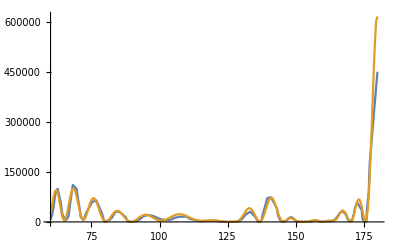

```mathematica
Plot[{datapaper[x],f632[x]},{x,60,180},PlotRange->All]
```

```mathematica
interv1=Table[{x, x + 5}, {x, 5, 90,5}];
interv2=Table[{x - 5, x + 5}, {x, 105, 174,10}]
intervals=Join[interv1,interv2]
```

{{100,110},{110,120},{120,130},{130,140},{140,150},{150,160},{160,170}}

{{5,10},{10,15},{15,20},{20,25},{25,30},{30,35},{35,40},{40,45},{45,50},{50,55},{55,60},{60,65},{65,70},{70,75},{75,80},{80,85},{85,90},{90,95},{100,110},{110,120},{120,130},{130,140},{140,150},{150,160},{160,170}}

```mathematica
f632[x_]:=fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi)
 locpaper=GoldenSearchMax[datapaper, #1, #2, 0.0005] & @@@ intervals
 locCST=GoldenSearchMax[f632, #1, #2, 0.0005] & @@@ intervals
 
 Mean[Abs[locpaper-locCST]]
```

```mathematica
f6320[x_]:=fInterp632LinearTsi[x*Pi/180,0]/(4 Pi)
 locpaper0=GoldenSearchMax[datapaper0, #1, #2, 0.0005] & @@@ intervals
 locCST0=GoldenSearchMax[f6320, #1, #2, 0.0005] & @@@ intervals
 
 Mean[Abs[locpaper0-locCST0]]
```

{5.65115,13.7952,17.618,21.4405,29.4183,33.0748,37.0635,41.2194,46.8699,51.8557,56.5094,62.6587,68.9748,70.0007,75.1249,80.0007,88.7537,90.0007,101.551,112.853,129.999,133.13,141.606,157.563,168.033}

{6.0001,13.9999,17.5003,21.5003,28.9999,33.4997,37.4997,42.,46.4995,51.0001,56.4995,62.,68.4997,70.0007,75.5004,80.0007,89.4996,90.0007,100.5,111.5,125.,133.5,141.499,156.5,167.5}

0.630358

```mathematica
Abs[datapaper0[50]-(fInterp632LinearTsi[50*Pi/180,0]/(4 Pi))]
```

```mathematica
fInterp632LinearTsi[50*Pi/180,0]/(4 Pi)
datapaper0[50]
```

39883.2

21681.8

```mathematica
Mean[Table[Abs[datapaper0[x]-(fInterp632LinearTsi[x*Pi/180,0]/(4 Pi))],{x,0,180}]]
Mean[Table[Abs[datapaper[x]-(fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi))],{x,0,180}]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

4.56462×10^7

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

2.65315×10^7

```mathematica
datapaper0[0]
fInterp632LinearTsi[0*Pi/180,0]/(4 Pi)
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.24542×10^10

1.58778×10^10

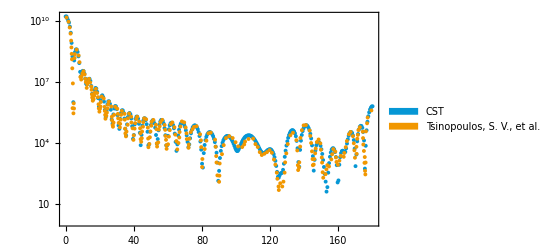

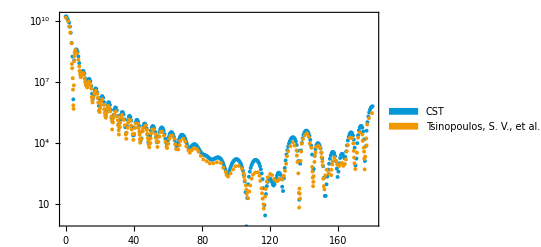

```mathematica
comparacionpaper90=ListPlot[{dataFF632Pi2DegreeLinearTsi,datapaper},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","Tsinopoulos, S. V., et al. 2002"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      
                      Evaluate[Sequence @@ plotStyling]]
comparacionpaper0=ListPlot[{dataFF6320DegreeLinearTsi,datapaper0},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","Tsinopoulos, S. V., et al. 2002"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["comparacionpaper90.svg",comparacionpaper90]
Export["comparacionpaper0.svg",comparacionpaper0]
```

comparacionpaper90.svg

comparacionpaper0.svg

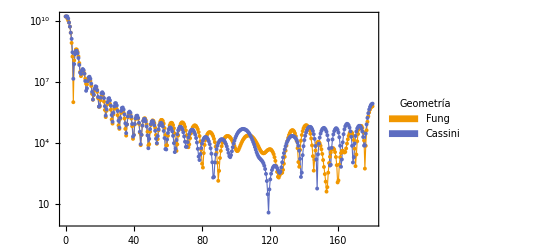

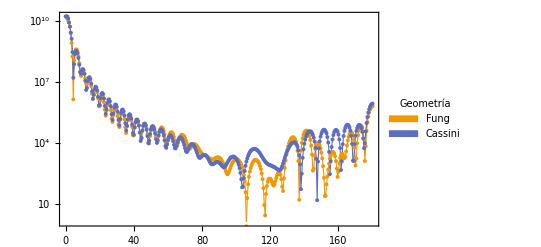

```mathematica
comparacionpaperCassini90=ListPlot[{dataFF632Pi2DegreeLinearTsi,dataFF632Pi2DegreeLinearTsiCass},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                       PlotRange->All,         
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"Fung","Cassini"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Joined->True,
                      Evaluate[Sequence @@ plotStyling]]
 
comparacionpaperCassini0=ListPlot[{dataFF6320DegreeLinearTsi,dataFF6320DegreeLinearTsiCass},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                       PlotRange->All,         
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"Fung","Cassini"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Joined->True,
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["comparacionpaperCassini90.svg",comparacionpaperCassini90]
Export["comparacionpaperCassini0.svg",comparacionpaperCassini0]
```

comparacionpaperCassini90.svg

comparacionpaperCassini0.svg

```mathematica
intervFront=Table[{x, x + 5}, {x, 5, 40,5}];
intervRetro=Table[{x, x + 5}, {x, 135, 175,5}];
intervLat=Table[{x - 5, x + 5}, {x, 50, 130,10}];
intervals=Join[intervFront,intervLat,intervRetro]
```

{{5,10},{10,15},{15,20},{20,25},{25,30},{30,35},{35,40},{40,45},{45,55},{55,65},{65,75},{75,85},{85,95},{95,105},{105,115},{115,125},{125,135},{135,140},{140,145},{145,150},{150,155},{155,160},{160,165},{165,170},{170,175},{175,180}}

```mathematica
cassini632[x_]:=fInterp632LinearTsiCass[x*Pi/180,Pi/2]/(4 Pi)
 cassiniMax=GoldenSearchMax[cassini632, #1, #2, 0.0005] & @@@ intervFront
 tsi632[x_]:=fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi)
 tsiMax=GoldenSearchMax[tsi632, #1, #2, 0.0005] & @@@ intervFront
 
 Mean[Abs[cassiniMax-tsiMax]]
```

{6.49947,13.9999,17.5003,21.5003,29.4996,33.4997,37.4997,42.}

{6.49947,13.9999,17.5003,21.5003,28.9999,33.4997,37.4997,42.}

0.0624624

```mathematica
cassini632[x_]:=fInterp632LinearTsiCass[x*Pi/180,Pi/2]/(4 Pi)
 cassiniMax=GoldenSearchMax[cassini632, #1, #2, 0.0005] & @@@ intervRetro
 tsi632[x_]:=fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi)
 tsiMax=GoldenSearchMax[tsi632, #1, #2, 0.0005] & @@@ intervRetro
 
 Mean[Abs[cassiniMax-tsiMax]]
```

{135.001,143.5,149.999,151.5,158.501,164.999,165.001,172.5,179.999}

{139.999,141.,148.,150.001,157.,162.5,167.5,173.,179.999}

1.99961

```mathematica
cassini632[x_]:=fInterp632LinearTsiCass[x*Pi/180,Pi/2]/(4 Pi)
 cassiniMax=GoldenSearchMax[cassini632, #1, #2, 0.0005] & @@@ intervRetro
 tsi632[x_]:=fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi)
 tsiMax=GoldenSearchMax[tsi632, #1, #2, 0.0005] & @@@ intervRetro
 
 Mean[Abs[cassiniMax-tsiMax]]
```

```mathematica
cassini632[x_]:=fInterp632LinearTsiCass[x*Pi/180,Pi/2]/(4 Pi)
 cassiniMax=GoldenSearchMax[cassini632, #1, #2, 0.0005] & @@@ intervLat
 tsi632[x_]:=fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi)
 tsiMax=GoldenSearchMax[tsi632, #1, #2, 0.0005] & @@@ intervLat
 
 Mean[Abs[cassiniMax-tsiMax]]
```

{50.9994,61.5002,67.4994,81.9999,91.9999,104.,105.001,122.501,132.999}

{51.0005,61.9999,68.4998,75.9996,94.9991,95.0009,107.999,120.,133.}

2.77777

## Esferocito

#### Convergencia numérica

```mathematica
dataEsfCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Cabs_12_11_10.csv"];
dataEsfCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Csca_12_11_10.csv"];

dataQabsEsf=Transpose[{dataEsfCabs[[All,1]],dataEsfCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
dataQscaEsf=Transpose[{dataEsfCsca[[All,1]],dataEsfCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
dataCabsEsf=Transpose[{dataEsfCabs[[All,1]],dataEsfCabs[[All,#]]}]&/@Range[2,4];
dataCscaEsf=Transpose[{dataEsfCsca[[All,1]],dataEsfCsca[[All,#]]}]&/@Range[2,4];
```

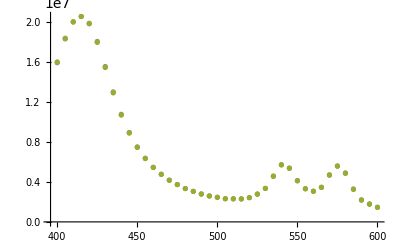

```mathematica
ListPlot[dataCabsEsf]
```

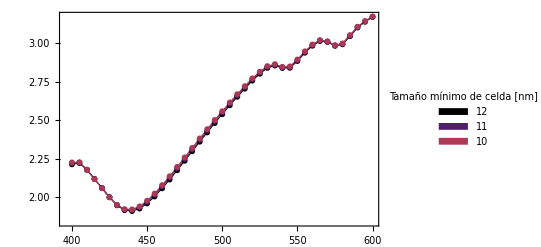

```mathematica
plotEsferocitoConv=ListPlot[dataQext[dataQabsEsf[[#]],dataQscaEsf[[#]]]&/@Range[1,3],PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12","11","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.35,0.8}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

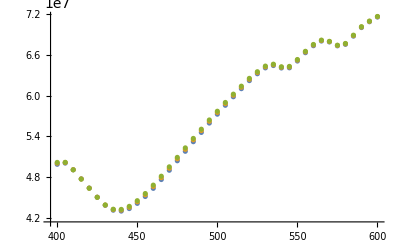

```mathematica
ListPlot[dataQext[dataCabsEsf[[#]],dataCscaEsf[[#]]]&/@Range[1,3]]
```

```mathematica
Export["EsferocitoConv.svg",plotEsferocitoConv]
```

EsferocitoConv.svg

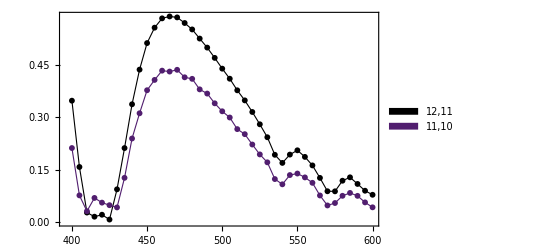

```mathematica
plotEsferocitoConvDif=ListPlot[{Transpose[{dataQext[dataQabsEsf[[1]],dataQscaEsf[[1]]][[All,1]],
                                          errorRel[dataQext[dataQabsEsf[[1]],dataQscaEsf[[1]]][[All,2]],dataQext[dataQabsEsf[[2]],dataQscaEsf[[2]]][[All,2]]]}],
                                          
                                 Transpose[{dataQext[dataQabsEsf[[2]],dataQscaEsf[[2]]][[All,1]],
                                          errorRel[dataQext[dataQabsEsf[[2]],dataQscaEsf[[2]]][[All,2]],dataQext[dataQabsEsf[[3]],dataQscaEsf[[3]]][[All,2]]]}]},
                            PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12,11","11,10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.85,0.8}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      FrameLabel->{{Style[MaTeX["\\text{Error relativo } Q_{\\text{ext}}[\%] "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["EsferocitoConvDif.svg",plotEsferocitoConvDif]
```

EsferocitoConvDif.svg

#### Datos Nature

```mathematica
dataEriSanonNature=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Nature_article.csv"];
dataCextEriSanoNature1=Transpose[{dataEriSanonNature[[All,1]],dataEriSanonNature[[All,2]]*10^6}];
dataCextEriSanoNature2=Transpose[{dataEriSanonNature[[All,1]],dataEriSanonNature[[All,4]]*10^6}];
dataCextEriSanoNature3=Transpose[{dataEriSanonNature[[All,1]],dataEriSanonNature[[All,6]]*10^6}];
```

```mathematica
datosNatureEPS=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Funciones_dielectricas\\epsEritrocitosData32lambda.csv"];
datosEPSNature=Interpolation[Transpose[{datosNatureEPS[[All,1]],Sqrt[datosNatureEPS[[All,2]]+ I datosNatureEPS[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
datosEPSNature[480]
```

1.42797+0.0014665 ⅈ

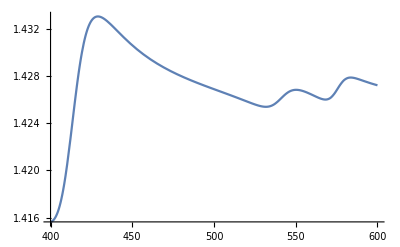

```mathematica
Plot[Re[datosEPSNature[l]],{l,400,600}]
```

```mathematica
eriQabsMieNature=Table[{λ,mieQabs[datosEPSNature[λ],1.339,2738.23,λ][[4]]},{λ,400,600,1}];
eriQscaMieNature=Table[{λ,mieQsca[datosEPSNature[λ],1.339,2738.23,λ][[4]]},{λ,400,600,1}];
```

```mathematica
eriQextMieNature=Table[{λ,mieQext[datosEPSNature[λ],1.339,2738.23,λ][[4]]},{λ,dataEsf[[All,1]]}];
```

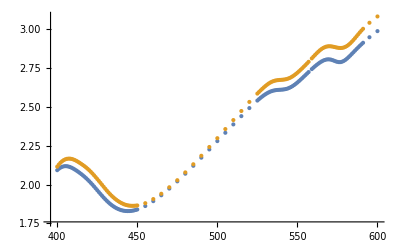

```mathematica
ListPlot[{eriQextMieNature,dataQext[dataQabsEsfFinal,dataQscaEsfFinal]}]
```

```mathematica
Mean[Abs[eriQextMieNature[[All,2]]-dataQext[dataQabsEsfFinal,dataQscaEsfFinal][[All,2]]]]
```

0.0592951

```mathematica
Length[dataEsfCabs[[All,1]]]
Length[dataEsf[[All,1]]]
```

41

77

```mathematica
dataEsfCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Cabs_12_11_10.csv"];
dataEsfCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Csca_12_11_10.csv"];

dataQabsEsf=Transpose[{dataEsfCabs[[All,1]],dataEsfCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
dataQscaEsf=Transpose[{dataEsfCsca[[All,1]],dataEsfCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];


dataEsf=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_nature_Cabs_2.csv"];
dataQabsEsfFinal=Transpose[{dataEsf[[All,1]],dataEsf[[All,2]]/(Pi*2680^2)}];
dataQscaEsfFinal=Transpose[{dataEsf[[All,1]],dataEsf[[All,3]]/(Pi*2680^2)}];
dataCabsEsfFinal=Transpose[{dataEsf[[All,1]],dataEsf[[All,2]]}];
dataCscaEsfFinal=Transpose[{dataEsf[[All,1]],dataEsf[[All,3]]}];

dataEsfFF440=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Esferocito_farfield_440.csv"];

dataThetaEsf=Drop[dataEsfFF440,1][[All,1]];
dataPhiEsf=Drop[dataEsfFF440,1][[All,2]];
dataRCSEsf=Drop[dataEsfFF440,1][[All,3]];

data440Esf = Transpose[{dataThetaEsf *Pi/180, dataPhiEsf*Pi/180, dataRCSEsf}];
fInterp440Esf = Interpolation[data440Esf,InterpolationOrder->1];
data440EsfLinear = Transpose[{dataThetaEsf *Pi/180, dataPhiEsf*Pi/180, 10^(dataRCSEsf/10)}];
fInterp440EsfLinear = Interpolation[data440EsfLinear,InterpolationOrder->1];


(*data440LinearEsf = Transpose[{dataThetaEsf *Pi/180, dataPhiEsf*Pi/180, 10^(dataRCSEsf/10)}];
fInterp440LinearEsf = Interpolation[data440LinearEsf,InterpolationOrder->1];*)
min440Esf = Min[dataRCSEsf];
max440Esf = Max[dataRCSEsf];
```

```mathematica
eriCextMie=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
```

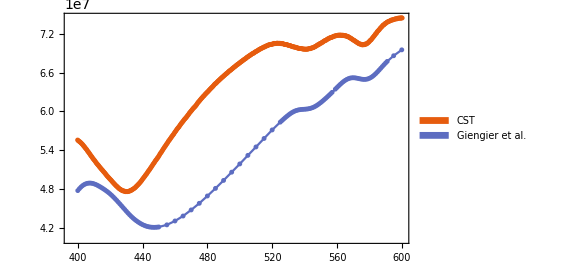

```mathematica
ListPlot[{dataCextEriSanoNature3,dataQext[dataCabsEsfFinal,dataCscaEsfFinal]},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->All,
                      PlotStyle -> colors,
                      FrameLabel->{{Style[MaTeX["C_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","Giengier et al."},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.25,0.83}],
                       ImagePadding->{{90,10},{50,50}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
fInterp440Esf[0.5*Pi/180,0]
```

107.3

```mathematica
dataFF4400EsfDif=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], 0]-fInterp440[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi, 2 Pi/120}];
dataFF44000EsfDif=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]-fInterp440[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi, 2 Pi/120}];

dataFF4400Esf=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi, 2 Pi/360}];
dataFF4400Pi2Esf=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi, 2 Pi/360}];
dataFF4400PiEsf=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0,  2 Pi, 2 Pi/360}];
dataFF4400PiEsfLinear=Table[{th,fInterp440EsfLinear[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0,  2 Pi, 2 Pi/360}];
```

InterpolatingFunction::femdmval: Input value {0.,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {3.14159,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,1.5708} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

InterpolatingFunction::femdmval: Input value {0.,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {3.14159,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,1.5708} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

InterpolatingFunction::femdmval: Input value {0.,3.14159} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {3.14159,3.14159} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,3.14159} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

InterpolatingFunction::femdmval: Input value {0.,3.14159} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {3.14159,3.14159} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,3.14159} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

```mathematica
dataFF440Pi2EsfDegree=Table[{th*180/Pi,fInterp440Esf[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF440Pi2EsfDegreeLinear=Table[{th*180/Pi,fInterp440EsfLinear[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
```

InterpolatingFunction::femdmval: Input value {0.,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {3.14159,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {3.14159,1.5708} lies outside the range of data in the interpolating function.

```mathematica
dataQext[dataQabsEsf,dataQscaEsf]
```

{{{400,0.705005},{810,2.2203}},{{400,0.707232},{810,2.2238}},{{400,0.708864},{810,2.22549}}}

#### Importación y preparación de datos

```mathematica
dataEsf=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Esferocito_Cabs_Csca.csv"];

dataQabsEsfFinal=Transpose[{dataEsf[[All,1]],dataEsf[[All,2]]/(Pi*2680^2)}];
dataQscaEsfFinal=Transpose[{dataEsf[[All,1]],dataEsf[[All,3]]/(Pi*2680^2)}];
dataCabsEsfFinal=Transpose[{dataEsf[[All,1]],dataEsf[[All,2]]}];
dataCscaEsfFinal=Transpose[{dataEsf[[All,1]],dataEsf[[All,3]]}];
```

#### Qext

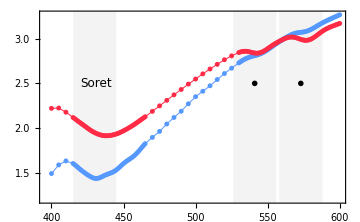

```mathematica
qExt34=ListPlot[{dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal],dataQext[dataQabsEsfFinal,dataQscaEsfFinal]},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.2,Automatic}},
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                       Prolog -> {
                      {
                      FaceForm[Directive[LightGray, Opacity[0.3]]],  EdgeForm[Transparent], Rectangle[{415, 0}, {445, 3.5}],Rectangle[{526, 0}, {556, 3.5}],Rectangle[{558, 0}, {588, 3.5}] },
                      Text[Style["Soret", 12, FontFamily->"Latin Modern Roman 10"],  {431, 2.5}],Text[Style[MaTeX["\\beta"], Magnification->1.05, FontFamily->"Latin Modern Roman 10"],  {541, 2.5}],
                      Text[Style[Style[MaTeX["\\alpha"], Magnification->1.05, FontFamily->"Latin Modern Roman 10"]],  {573, 2.5}] },
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["Qext_Esf.svg",qExt34]
```

Qext_Esf.svg

```mathematica
MinimalBy[dataQext[dataQabsEsfFinal,dataQscaEsfFinal],Last]
```

```mathematica
dataQext[dataQabsEsfFinal,dataQscaEsfFinal][[All,2]]-dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal][[All,2]]
```

{0.730419,0.637303,0.546119,0.515337,0.515391,0.516468,0.518148,0.520056,0.521856,0.523265,0.524083,0.524229,0.523758,0.522825,0.521587,0.520083,0.518134,0.515337,0.51116,0.505131,0.497046,0.487102,0.47591,0.464368,0.453439,0.443912,0.436214,0.430339,0.425892,0.422218,0.418581,0.414339,0.409077,0.402679,0.395331,0.387467,0.379663,0.372505,0.366471,0.361831,0.3586,0.356552,0.355267,0.354218,0.35286,0.350715,0.347435,0.342847,0.336975,0.330049,0.322477,0.314798,0.307602,0.30143,0.291584,0.286149,0.264901,0.253491,0.244075,0.220683,0.198614,0.194961,0.188162,0.170142,0.154364,0.137909,0.116352,0.110643,0.104263,0.0971746,0.089394,0.0810001,0.0721396,0.0630253,0.0539254,0.0451416,0.0369858,0.0297455,0.0236497,0.0188436,0.0153665,0.013147,0.0120109,0.0117053,0.0119319,0.0123871,0.0127994,0.0129618,0.0127484,0.0121169,0.0110971,0.00976605,0.00821658,0.00652621,0.00473069,0.00280965,0.000684541,-0.00177263,-0.00471522,-0.00829892,-0.0126513,-0.0178503,-0.023907,-0.0307616,-0.0382857,-0.0462967,-0.0545742,-0.0628798,-0.0709766,-0.0786427,-0.0856849,-0.091941,-0.0972836,-0.101622,-0.1049,-0.107098,-0.108232,-0.108359,-0.107576,-0.106019,-0.103864,-0.101313,-0.0985857,-0.0959032,-0.0934699,-0.0914564,-0.0899856,-0.0891218,-0.0888669,-0.0891672,-0.0899209,-0.0909958,-0.0922481,-0.0935417,-0.0947662,-0.0958499,-0.0967644}

```mathematica
dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal][[All,1]][[-40]]
```

561

### lambda = 431 nm

```mathematica
dataEsfFF431=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Esferocito_farfield_431.csv"];

dataThetaEsf431=Drop[dataEsfFF431,1][[All,1]];
dataPhiEsf431=Drop[dataEsfFF431,1][[All,2]];
dataRCSEsf431=Drop[dataEsfFF431,1][[All,3]];

data431Esf = Transpose[{dataThetaEsf431 *Pi/180, dataPhiEsf431*Pi/180, dataRCSEsf431}];
data431LinearEsf = Transpose[{dataThetaEsf431 *Pi/180, dataPhiEsf431*Pi/180, 10^(dataRCSEsf431/10)}];
fInterp431Esf = Interpolation[data431Esf,InterpolationOrder->1];
fInterp431LinearEsf = Interpolation[data431LinearEsf,InterpolationOrder->1];
min431Esf = Min[dataRCSEsf431];
max431Esf = Max[dataRCSEsf431];
```

```mathematica
dataFF4310Esf=Table[{th,fInterp431Esf[Abs[If[th > Pi, th - 2 Pi, th]], 0]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF431PiEsf=Table[{th,fInterp431Esf[Abs[If[th > Pi, th - 2 Pi, th]], Pi]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF431Pi2Esf=Table[{th,fInterp431Esf[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]/(4 Pi)}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF431PiDegreeEsf=Table[{th*180/Pi,fInterp431Esf[th, Pi]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF431Pi2DegreeLinearEsf=Table[{th*180/Pi,fInterp431LinearEsf[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF4310DegreeLinearEsf=Table[{th*180/Pi,fInterp431LinearEsf[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

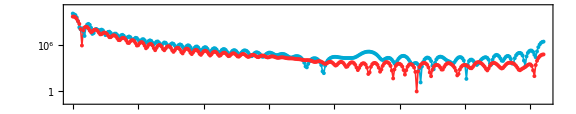

```mathematica
linearplot431FFEsf1=ListPlot[{dataFF4310DegreeLinear, dataFF4310DegreeLinearEsf},PlotMarkers->{"●",4},
                      Joined->True,
                      ScalingFunctions->"Log",
                      PlotRange->{{Automatic,Automatic},{10^(-1.5),10^(11)}},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1]&/@{MaTeX["\\varphi=0^{\\circ}"],
                                                                                                                      MaTeX["\\varphi=0^{\\circ}"]},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",4},
                                    LegendMargins->0,
                                    
                                    Spacings->0.05],{0.5,0.8}],
                      PlotStyle -> {Directive[colorsCHCM[[1]], Thickness[0.002]],Directive[redlight34, Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{nm}^2] "],Magnification->1.05],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.05],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Large,
                      AspectRatio->2/10,
                      FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.25],
                      Evaluate[Sequence @@ plotStyling]]
```

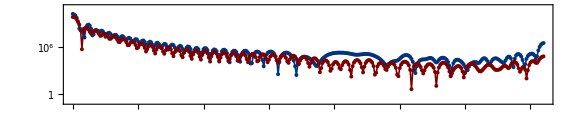

```mathematica
linearplot431FFEsf2=ListPlot[{dataFF431Pi2DegreeLinear,dataFF431Pi2DegreeLinearEsf},PlotMarkers->{"●",4},
                      Joined->True,
                      ScalingFunctions->"Log",
                      PlotRange->{{Automatic,Automatic},{10^(-1),10^(11)}},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1]&/@{MaTeX["\\varphi=90^{\\circ}"],
                                                                                                                      MaTeX["\\varphi=90^{\\circ}"]},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",4},
                                    LegendMargins->0,
                                    
                                    Spacings->0.05],{0.5,0.8}],
                      PlotStyle -> {Directive[colorsCHCM[[2]], Thickness[0.002]],Directive[reddark34, Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{nm}^2] "],Magnification->1.05],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.05],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Large,
                      AspectRatio->2/10,
                      FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.25],
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["linearplot431FFEsf1.svg",linearplot431FFEsf1]
Export["linearplot431FFEsf2.svg",linearplot431FFEsf2]
```

linearplot431FFEsf1.svg

linearplot431FFEsf2.svg

```mathematica
polarplot431FFCompEsfEri=ListPolarPlot[
 {dataFF4310, dataFF431Pi2,dataFF4310Esf,dataFF431Pi2Esf},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 2, 4, 6, 8, 10}
 },

 PlotLegends -> Placed[SwatchLegend[
   {
    Style[MaTeX["\\varphi=0"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=\\pi/2"], Magnification -> 1.7],
    Style[MaTeX["\\varphi=0"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=\\pi/2"], Magnification -> 1.7]
   }],
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},
Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-15.0,0},{-15.0,10}}],

 (* ticks *)
   Table[   Line[{     {-15.3,r},     { -15.0,r}   }],
   {r,0,10,2}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-15.15,r},{ -15,r}}], {r,0,10,0.5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-16.5,r} ], {r,0,10,2}],
     Text[Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{dB}] "], Magnification->1.8],  {-16,12.0} ]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {bluelight30,bluedark30,redlight34,reddark34}),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 12
]
```

-Graphics-

```mathematica
Export["polarplot431FFComEsfEri.svg",polarplot431FFCompEsfEri]
```

polarplot431FFComEsfEri.svg

```mathematica
cf431Esf = ColorMapSuite["lajolla"];
```

```mathematica
plotEsf431axes=SphericalPlot3D[
 fInterp431Esf[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
 PlotPoints -> 100,

 ColorFunction -> Function[{x, y, z, th, ph},
   cf431Esf[
     Rescale[
       fInterp431Esf[th, ph],
       {min431Esf, max431Esf}
     ]
   ]
 ],
 ColorFunctionScaling -> False,

 PlotStyle -> Opacity[1],
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 Mesh -> False,
 Exclusions -> None,

PlotLegends -> BarLegend[
 {cf431Esf, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,\\,\\, "],Magnification->1.4]
],
 LabelStyle -> {
   Black,
   FontFamily -> "Latin Modern Roman 10",
   FontSize -> 18
 },
  ViewPoint -> {1, 12, 0}, 
  ViewVertical -> {0, -1, 0}
]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
plotEsf431noaxes0=SphericalPlot3D[fInterp431Esf[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
  ColorFunction -> Function[{x, y, z, th, ph},
   cf431Esf[
     Rescale[
       fInterp431Esf[th, ph],
       {min431Esf, max431Esf}
     ]
   ]
 ],
 
 ColorFunctionScaling -> False,
 
 PlotPoints -> 100,
 Boxed -> False,
 Axes -> False,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 
PlotLegends -> Placed[BarLegend[
 {cf431Esf, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["(\\text{d}C_{\\text{sca}}/\\text{d}\\Omega)/(\\text{d}C_{\\text{sca}}/\\text{d}\\Omega)_{\\text{max}}\\,\\,\\, "],
 Magnification->1.6]
],Top],
   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->20},
   ViewPoint -> {1, 1, 0}, 
  ViewVertical -> {0, -1, 0}
 ];

planeX=ParametricPlot3D[{0,y,z},{y,-100,100},{z,-100,120},PlotStyle->Directive[RGBColor[80/255,45/255,22/255],Opacity[0.3]],Mesh->None];

planeY=ParametricPlot3D[{x,0,z},{x,-100,100},{z,-100,120},PlotStyle->Directive[Red,Opacity[0.25]],Mesh->None];

plotEsf431noaxes=Show[plotEsf431noaxes0,planeX,planeY,PlotRange->All,Lighting -> {
   {"Directional", White, {-1, 0, 0}}
}]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Export["FFdistribution431_Esf.svg",plotEsf431noaxes]
Export["FFdistribution431axes_Esf.svg",plotEsf431axes]
```

FFdistribution431_Esf.svg

FFdistribution431axes_Esf.svg

### Cálculo de propiedades

#### Desfases

```mathematica
interv1=Table[{x, x + 2}, {x, 0, 98,2}]
interv2=Table[{x - 2, x}, {x, 102, 178,2}]
intervals=Join[interv1,interv2]
```

{{0,2},{2,4},{4,6},{6,8},{8,10},{10,12},{12,14},{14,16},{16,18},{18,20},{20,22},{22,24},{24,26},{26,28},{28,30},{30,32},{32,34},{34,36},{36,38},{38,40},{40,42},{42,44},{44,46},{46,48},{48,50},{50,52},{52,54},{54,56},{56,58},{58,60},{60,62},{62,64},{64,66},{66,68},{68,70},{70,72},{72,74},{74,76},{76,78},{78,80},{80,82},{82,84},{84,86},{86,88},{88,90},{90,92},{92,94},{94,96},{96,98},{98,100}}

{{100,102},{102,104},{104,106},{106,108},{108,110},{110,112},{112,114},{114,116},{116,118},{118,120},{120,122},{122,124},{124,126},{126,128},{128,130},{130,132},{132,134},{134,136},{136,138},{138,140},{140,142},{142,144},{144,146},{146,148},{148,150},{150,152},{152,154},{154,156},{156,158},{158,160},{160,162},{162,164},{164,166},{166,168},{168,170},{170,172},{172,174},{174,176},{176,178}}

{{0,2},{2,4},{4,6},{6,8},{8,10},{10,12},{12,14},{14,16},{16,18},{18,20},{20,22},{22,24},{24,26},{26,28},{28,30},{30,32},{32,34},{34,36},{36,38},{38,40},{40,42},{42,44},{44,46},{46,48},{48,50},{50,52},{52,54},{54,56},{56,58},{58,60},{60,62},{62,64},{64,66},{66,68},{68,70},{70,72},{72,74},{74,76},{76,78},{78,80},{80,82},{82,84},{84,86},{86,88},{88,90},{90,92},{92,94},{94,96},{96,98},{98,100},{100,102},{102,104},{104,106},{106,108},{108,110},{110,112},{112,114},{114,116},{116,118},{118,120},{120,122},{122,124},{124,126},{126,128},{128,130},{130,132},{132,134},{134,136},{136,138},{138,140},{140,142},{142,144},{144,146},{146,148},{148,150},{150,152},{152,154},{154,156},{156,158},{158,160},{160,162},{162,164},{164,166},{166,168},{168,170},{170,172},{172,174},{174,176},{176,178}}

```mathematica
interv1=Table[{x, x + 3}, {x, 0, 57,3}]
interv2=Table[{x - 5, x}, {x, 125, 175,5}]
```

{{0,3},{3,6},{6,9},{9,12},{12,15},{15,18},{18,21},{21,24},{24,27},{27,30},{30,33},{33,36},{36,39},{39,42},{42,45},{45,48},{48,51},{51,54},{54,57},{57,60}}

{{120,125},{125,130},{130,135},{135,140},{140,145},{145,150},{150,155},{155,160},{160,165},{165,170},{170,175}}

```mathematica
f431Pi2Esf[x_]:=fInterp431LinearEsf[x*Pi/180,Pi/2]/(4 Pi)
 f431Pi2Eri[x_]:=fInterp431Linear[x*Pi/180,Pi/2]/(4 Pi)
 locf431Pi2Esf=GoldenSectionSearchMax[f431Pi2Esf, #1, #2, 0.0005] & @@@ interv1
 locf431Pi2Eri=GoldenSectionSearchMax[f431Pi2Eri, #1, #2, 0.0005] & @@@ interv1
 
 Mean[Abs[locf431Pi2Esf-locf431Pi2Eri]]
```

{0.499514,4.99977,8.49997,9.00068,12.0007,15.5,19.4996,22.9998,26.5,29.5005,32.9993,33.0007,36.5,40.0002,43.5004,46.9998,50.5,53.9993,54.0007,58.0002}

{0.000679656,5.99932,6.00068,10.9998,13.9998,16.4996,19.0002,21.5,24.0007,29.5,32.5,34.9998,37.9998,40.9998,43.9998,47.5,50.5005,51.0007,54.0007,58.0002}

1.12454

```mathematica
f4310Esf[x_]:=fInterp431LinearEsf[x*Pi/180,0]/(4 Pi)
 f4310Eri[x_]:=fInterp431Linear[x*Pi/180,0]/(4 Pi)
 locf4310Esf=GoldenSectionSearchMax[f4310Esf, #1, #2, 0.0005] & @@@ interv1
 locf4310Eri=GoldenSectionSearchMax[f4310Eri, #1, #2, 0.0005] & @@@ interv1
 
 Mean[Abs[locf4310Esf-locf4310Eri]]
```

{0.499514,4.99977,8.49997,9.00068,12.0007,15.5,19.4996,22.9998,26.5,29.5005,32.9993,33.0007,36.5,40.0002,43.5004,46.9998,50.5,51.0007,54.4995,58.0002}

{0.000679656,5.99932,6.00068,10.9998,13.9998,16.4996,19.0002,21.5,24.0007,29.5,32.5,34.9998,37.9998,40.9998,43.9998,47.5,50.5,53.9993,54.0007,57.9994}

1.14949

#### Factor de anisotropía

```mathematica
fInterp431LinearEsf = Interpolation[data431LinearEsf];
CscaInt431Esf = NIntegrate[(fInterp431LinearEsf[th, phi]/(4 Pi))* Sin[th], {th, 0, Pi}, {phi, 0, 2 Pi}];

g431Esf = NIntegrate[ (fInterp431LinearEsf[th, phi]/(4 Pi))* Cos[th]*Sin[th],{th, 0, Pi},{phi, 0, 2 Pi}]/CscaInt431Esf
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.88024×10^7 and 4788.62 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.8244×10^7 and 3598.84 for the integral and error estimates.

0.980614

```mathematica
CscaInt431
```

4.98933×10^7

#### Correlaciones

```mathematica
fInterp431LinearEsf = Interpolation[data431LinearEsf,InterpolationOrder->1];

dataFF431Pi2DegreeLinearFrontEsf=Table[fInterp431LinearEsf[th, Pi/2]/(4 Pi), {th, 0,  Pi/3,  Pi/60}];
dataFF431Pi2DegreeLinearLatEsf=Table[fInterp431LinearEsf[th, Pi/2]/(4 Pi), {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF431Pi2DegreeLinearRetroEsf=Table[fInterp431LinearEsf[th, Pi/2]/(4 Pi), {th, 2 Pi/3,  Pi,  Pi/60}];

dataFF4310DegreeLinearFrontEsf=Table[fInterp431LinearEsf[th, 0]/(4 Pi), {th, 0,  Pi/3,  Pi/60}];
dataFF4310DegreeLinearLatEsf=Table[fInterp431LinearEsf[th, 0]/(4 Pi), {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF4310DegreeLinearRetroEsf=Table[fInterp431LinearEsf[th, 0]/(4 Pi), {th, 2 Pi/3,  Pi,  Pi/60}];
```

```mathematica
N[Correlation[dataFF4310DegreeLinearFrontEsf,dataFF431Pi2DegreeLinearFrontEsf],20]
Correlation[dataFF4310DegreeLinearLatEsf,dataFF431Pi2DegreeLinearLatEsf]
Correlation[dataFF4310DegreeLinearRetroEsf,dataFF431Pi2DegreeLinearRetroEsf]
```

1.

0.777199

0.949769

#### Contribuciones integradas

```mathematica
CscaInt431Front0Esf = NIntegrate[(fInterp431LinearEsf[th, 0]/(4 Pi))* Sin[th], {th, 0, Pi/3}]
CscaInt431FrontPi2Esf= NIntegrate[(fInterp431LinearEsf[th, Pi/2]/(4 Pi))* Sin[th], {th, 0, Pi/3}]

CscaInt431FrontDifEsf=100*Abs[CscaInt431Front0Esf-CscaInt431FrontPi2Esf]/CscaInt431Front0Esf

CscaInt431Lat0Esf = NIntegrate[(fInterp431LinearEsf[th, 0]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]
CscaInt431LatPi2Esf = NIntegrate[(fInterp431LinearEsf[th, Pi/2]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]

CscaInt431LatDifEsf=100*Abs[CscaInt431Lat0Esf-CscaInt431LatPi2Esf]/CscaInt431Lat0Esf

CscaInt431Retro0Esf = NIntegrate[(fInterp431LinearEsf[th, 0]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]
CscaInt431RetroPi2Esf = NIntegrate[(fInterp431LinearEsf[th, Pi/2]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]

CscaInt431RetroDifEsf=100*Abs[CscaInt431Retro0Esf-CscaInt431RetroPi2Esf]/CscaInt431Retro0Esf
```

4.58156×10^6

4.55571×10^6

0.564309

17161.8

32617.8

90.0599

1066.16

2034.79

90.8527

```mathematica
CscaInt431Front0Esf/(Pi * 2680^2)
CscaInt431Lat0Esf/(Pi * 2680^2)
CscaInt431Retro0Esf/(Pi * 2680^2)

CscaInt431FrontPi2Esf/(Pi * 2680^2)
CscaInt431LatPi2Esf/(Pi * 2680^2)
CscaInt431RetroPi2Esf/(Pi * 2680^2)
```

0.203046

0.000760578

0.00004725

0.2019

0.00144556

0.000090178

```mathematica
total0Esf=CscaInt431Front0Esf+CscaInt431Lat0Esf+CscaInt431Retro0Esf
CscaInt431Front0Esf/total0Esf
CscaInt431Lat0Esf/total0Esf
CscaInt431Retro0Esf/total0Esf
```

4.59979×10^6

0.996037

0.003731

0.000231784

```mathematica
Mea
```

```mathematica
Mean[{(CscaInt431Lat0Esf/total0Esf)/(CscaInt431Lat0/total0Eri),(CscaInt431LatPi2Esf/totalPi2Esf)/(CscaInt431LatPi2/totalPi2Eri)}]

Mean[{(CscaInt431Retro0Esf/total0Esf)/(CscaInt431Retro0/total0Eri),(CscaInt431RetroPi2Esf/totalPi2Esf)/(CscaInt431RetroPi2/totalPi2Eri)}]

Mean[{(CscaInt431Front0Esf/total0Esf)/(CscaInt431Front0/total0Eri),(CscaInt431FrontPi2Esf/totalPi2Esf)/(CscaInt431FrontPi2/totalPi2Eri)}]
```

0.58848

0.240923

1.00485

```mathematica
totalPi2Esf=CscaInt431FrontPi2Esf+CscaInt431LatPi2Esf+CscaInt431RetroPi2Esf
CscaInt431FrontPi2Esf/totalPi2Esf
CscaInt431LatPi2Esf/totalPi2Esf
CscaInt431RetroPi2Esf/totalPi2Esf
```

4.59036×10^6

0.992451

0.00710571

0.000443275

```mathematica
CscaInt541Front0 = NIntegrate[(fInterp541Linear[th, 0]/(4 Pi))* Sin[th], {th, 0, Pi/3}]
CscaInt541FrontPi2 = NIntegrate[(fInterp541Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, 0, Pi/3}]

CscaInt541FrontDif=100*Abs[CscaInt541Front0-CscaInt541FrontPi2]/CscaInt541Front0


CscaInt541Lat0 = NIntegrate[(fInterp541Linear[th, 0]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]
CscaInt541LatPi2 = NIntegrate[(fInterp541Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]

CscaInt541LatDif=100*Abs[CscaInt541Lat0-CscaInt541LatPi2]/CscaInt541Lat0


CscaInt541Retro0 = NIntegrate[(fInterp541Linear[th, 0]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]
CscaInt541RetroPi2 = NIntegrate[(fInterp541Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]

CscaInt541RetroDif=100*Abs[CscaInt541Retro0-CscaInt541RetroPi2]/CscaInt541Retro0
```

1.91037×10^7

1.89795×10^7

0.650345

66659.

92567.5

38.8671

47648.4

60836.2

27.6775

```mathematica
CscaInt541Front0/(Pi * 3750^2)
CscaInt541Lat0/(Pi * 3750^2)
CscaInt541Retro0/(Pi * 3750^2)

CscaInt541FrontPi2/(Pi * 3750^2)
CscaInt541LatPi2/(Pi * 3750^2)
CscaInt541RetroPi2/(Pi * 3750^2)
```

0.43242

0.00150885

0.00107854

0.429607

0.0020953

0.00137705

```mathematica
CscaInt573Front0 = NIntegrate[(fInterp573Linear[th, 0]/(4 Pi))* Sin[th], {th, 0, Pi/3}]
CscaInt573FrontPi2 = NIntegrate[(fInterp573Linear[th,Pi/2]/(4 Pi))* Sin[th], {th, 0, Pi/3}]

CscaInt573FrontDif=100*Abs[CscaInt573Front0-CscaInt573FrontPi2]/CscaInt573Front0

CscaInt573Lat0 = NIntegrate[(fInterp573Linear[th, 0]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]
CscaInt573LatPi2 = NIntegrate[(fInterp573Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]

CscaInt573LatDif=100*Abs[CscaInt573Lat0-CscaInt573LatPi2]/CscaInt573Lat0


CscaInt573Retro0 = NIntegrate[(fInterp573Linear[th, 0]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]
CscaInt573RetroPi2 = NIntegrate[(fInterp573Linear[th,Pi/2]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]

CscaInt573RetroDif=100*Abs[CscaInt573Retro0-CscaInt573RetroPi2]/CscaInt573Retro0
```

2.05433×10^7

2.04389×10^7

0.508157

56327.8

111729.

98.3554

10872.

15076.5

38.6723

```mathematica
CscaInt573Front0/(Pi * 3750^2)
CscaInt573Lat0/(Pi * 3750^2)
CscaInt573Retro0/(Pi * 3750^2)

CscaInt573FrontPi2/(Pi * 3750^2)
CscaInt573LatPi2/(Pi * 3750^2)
CscaInt573RetroPi2/(Pi * 3750^2)
```

0.465005

0.001275

0.000246093

0.462642

0.00252903

0.000341262

## Microcito

#### Convergencia numérica

```mathematica
dataEsfCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Cabs_12_11_10.csv"];
dataEsfCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Csca_12_11_10.csv"];

dataQabsEsf=Transpose[{dataEsfCabs[[All,1]],dataEsfCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
dataQscaEsf=Transpose[{dataEsfCsca[[All,1]],dataEsfCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
dataCabsEsf=Transpose[{dataEsfCabs[[All,1]],dataEsfCabs[[All,#]]}]&/@Range[2,4];
dataCscaEsf=Transpose[{dataEsfCsca[[All,1]],dataEsfCsca[[All,#]]}]&/@Range[2,4];
```

```mathematica
ListPlot[dataCabsEsf]
```

-Graphics-

```mathematica
plotEsferocitoConv=ListPlot[dataQext[dataQabsEsf[[#]],dataQscaEsf[[#]]]&/@Range[1,3],PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12","11","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.35,0.8}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

-Graphics-

```mathematica
ListPlot[dataQext[dataCabsEsf[[#]],dataCscaEsf[[#]]]&/@Range[1,3]]
```

-Graphics-

```mathematica
Export["EsferocitoConv.svg",plotEsferocitoConv]
```

EsferocitoConv.svg

```mathematica
plotEsferocitoConvDif=ListPlot[{Transpose[{dataQext[dataQabsEsf[[1]],dataQscaEsf[[1]]][[All,1]],
                                          errorRel[dataQext[dataQabsEsf[[1]],dataQscaEsf[[1]]][[All,2]],dataQext[dataQabsEsf[[2]],dataQscaEsf[[2]]][[All,2]]]}],
                                          
                                 Transpose[{dataQext[dataQabsEsf[[2]],dataQscaEsf[[2]]][[All,1]],
                                          errorRel[dataQext[dataQabsEsf[[2]],dataQscaEsf[[2]]][[All,2]],dataQext[dataQabsEsf[[3]],dataQscaEsf[[3]]][[All,2]]]}]},
                            PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12,11","11,10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.85,0.8}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      FrameLabel->{{Style[MaTeX["\\text{Error relativo } Q_{\\text{ext}}[\%] "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

-Graphics-

```mathematica
Export["EsferocitoConvDif.svg",plotEsferocitoConvDif]
```

EsferocitoConvDif.svg

#### Importación y preparación de datos

```mathematica
dataMicro=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Microcito_Cabs_Csca.csv"];

dataQabsMicroFinal=Transpose[{dataMicro[[All,1]],dataMicro[[All,2]]/(Pi*3486^2)}];
dataQscaMicroFinal=Transpose[{dataMicro[[All,1]],dataMicro[[All,3]]/(Pi*3486^2)}];
dataCabsMicroFinal=Transpose[{dataMicro[[All,1]],dataMicro[[All,2]]}];
dataCscaMicroFinal=Transpose[{dataMicro[[All,1]],dataMicro[[All,3]]}];
```

```mathematica
2.6*0.93
2.7*0.93
0.8128*0.93
```

2.418

2.511

0.755904

#### Qext

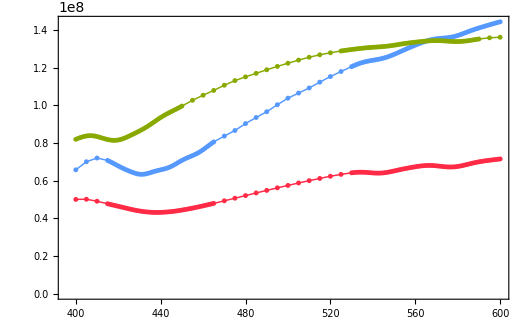

```mathematica
cExt28=ListPlot[{dataQext[dataCabsEriSanoFinal,dataCscaEriSanoFinal],dataQext[dataCabsEsfFinal,dataCscaEsfFinal],dataQext[dataCabsMicroFinal,dataCscaMicroFinal]},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.2,Automatic}},
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]],
                                          Directive[RGBColor[136/255,170/255,0/155], Thickness[0.002]],
                                                          },
                      FrameLabel->{{Style[MaTeX["C_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                      ImagePadding->{{100,10},{60,20}}
                   ,
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["Cext_Micro.svg",cExt28]
```

Cext_Micro.svg

```mathematica
dataCscaMicroFinal[[All,2]]/dataCabsMicroFinal[[All,2]]
```

{7.03826,6.6175,6.22488,5.86161,5.52829,5.22564,4.95505,4.71856,4.51853,4.35721,4.23637,4.15719,4.12042,4.12662,4.17644,4.27078,4.41075,4.5975,4.83185,5.11396,5.44317,5.8181,6.23709,6.6988,7.20283,7.74993,8.34181,8.98063,9.66835,10.4064,11.1957,12.0369,12.9306,13.877,14.8756,15.9242,17.0181,18.1507,19.3153,20.5075,21.7277,22.9823,24.2822,25.6401,27.066,28.5633,30.1272,31.7449,33.3992,35.0738,36.7571,45.3163,54.3612,65.1761,76.4452,87.2026,99.4265,111.86,123.04,131.108,142.055,149.122,153.29,151.996,145.177,134.046,130.357,126.185,121.643,116.86,111.953,107.012,102.088,97.2065,92.3765,87.6115,82.9412,78.4181,74.1158,70.1201,66.5172,63.3846,60.7849,58.7646,57.356,56.5808,56.4537,56.9842,58.1765,60.0254,62.5109,65.5883,69.1793,73.167,77.3967,81.6924,85.8843,89.8425,93.5034,96.8762,100.025,103.027,105.926,108.682,111.131,112.976,113.816,113.239,110.955,106.931,101.439,94.9905,88.1863,81.5707,75.5469,70.3629,66.1406,62.92,60.6993,59.4646,59.2095,59.9474,61.7187,64.5938,68.6727,74.0812,80.9565,89.4231,99.5511,111.296,124.429,189.526,227.104}

```mathematica
Mean[dataCscaMicroFinal[[All,2]]/dataCabsMicroFinal[[All,2]]]
```

62.1545

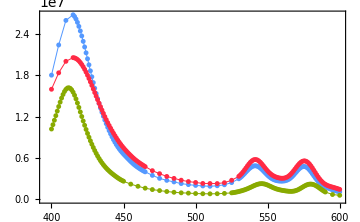

```mathematica
cAbs28=ListPlot[{dataCabsEriSanoFinal,dataCabsEsfFinal,dataCabsMicroFinal},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.2,Automatic}},
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]],
                                          Directive[RGBColor[136/255,170/255,0/155], Thickness[0.002]],
                                                          },
                      FrameLabel->{{Style[MaTeX["C_{\\text{abs}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                      ImagePadding->{{100,10},{60,20}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["Cabs_Micro.svg",cAbs28]
```

Cabs_Micro.svg

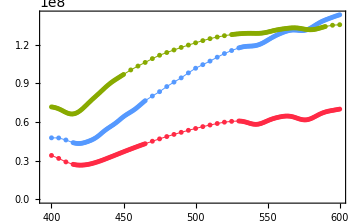

```mathematica
cSca28=ListPlot[{dataCscaEriSanoFinal,dataCscaEsfFinal,dataCscaMicroFinal},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.2,Automatic}},
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]],
                                          Directive[RGBColor[136/255,170/255,0/155], Thickness[0.002]],
                                                          },
                      FrameLabel->{{Style[MaTeX["C_{\\text{sca}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                       ImagePadding->{{100,10},{60,20}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["CscaMicro.svg",cSca28]
```

CscaMicro.svg

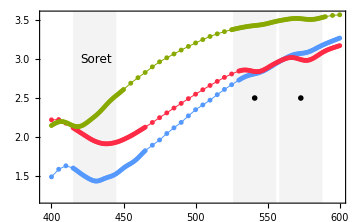

```mathematica
qExt28=ListPlot[{dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal],dataQext[dataQabsEsfFinal,dataQscaEsfFinal],dataQext[dataQabsMicroFinal,dataQscaMicroFinal]},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.2,Automatic}},
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]],
                                          Directive[RGBColor[136/255,170/255,0/155], Thickness[0.002]],
                                                          },
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                       Prolog -> {
                      {
                      FaceForm[Directive[LightGray, Opacity[0.3]]],  EdgeForm[Transparent], Rectangle[{415, 0}, {445, 3.9}],Rectangle[{526, 0}, {556, 3.9}],Rectangle[{558, 0}, {588, 3.9}] },
                      Text[Style["Soret", 12, FontFamily->"Latin Modern Roman 10"],  {431, 3}],Text[Style[MaTeX["\\beta"], Magnification->1.05, FontFamily->"Latin Modern Roman 10"],  {541, 2.5}],
                      Text[Style[Style[MaTeX["\\alpha"], Magnification->1.05, FontFamily->"Latin Modern Roman 10"]],  {573, 2.5}] },
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["Qext_Micro.svg",qExt28]
```

Qext_Micro.svg

```mathematica
MinimalBy[dataQext[dataQabsMicroFinal,dataQscaMicroFinal],Last]
```

{{418,2.13313}}

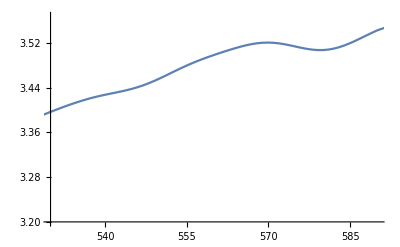

```mathematica
ListLinePlot[dataQext[dataQabsMicroFinal,dataQscaMicroFinal],PlotRange->{{530,590},{3.2,Automatic}}]
```

```mathematica
dataQext[dataQabsMicroFinal,dataQscaMicroFinal]
```

{{400,2.14753},{401,2.15964},{402,2.17053},{403,2.18011},{404,2.1881},{405,2.1941},{406,2.19772},{407,2.19868},{408,2.19693},{409,2.19266},{410,2.18627},{411,2.17837},{412,2.1696},{413,2.16063},{414,2.15209},{415,2.14457},{416,2.13859},{417,2.13465},{418,2.13313},{419,2.13431},{420,2.13827},{421,2.14493},{422,2.15401},{423,2.16508},{424,2.17762},{425,2.19112},{426,2.20517},{427,2.21948},{428,2.23392},{429,2.24854},{430,2.26351},{431,2.27906},{432,2.29545},{433,2.31284},{434,2.33128},{435,2.3507},{436,2.37083},{437,2.39133},{438,2.41178},{439,2.43175},{440,2.45093},{441,2.4691},{442,2.48621},{443,2.50238},{444,2.51781},{445,2.5328},{446,2.54764},{447,2.56259},{448,2.57783},{449,2.59344},{450,2.60942},{455,2.69021},{460,2.7607},{465,2.82735},{470,2.89959},{475,2.96412},{480,3.01612},{485,3.06498},{490,3.11488},{495,3.16157},{500,3.20606},{505,3.24932},{510,3.28912},{515,3.32296},{520,3.35113},{525,3.37578},{526,3.38025},{527,3.38456},{528,3.38871},{529,3.39272},{530,3.3966},{531,3.40038},{532,3.40405},{533,3.40759},{534,3.41101},{535,3.41425},{536,3.4173},{537,3.42012},{538,3.4227},{539,3.42505},{540,3.4272},{541,3.42922},{542,3.4312},{543,3.43324},{544,3.43545},{545,3.43794},{546,3.44079},{547,3.44405},{548,3.44773},{549,3.45181},{550,3.4562},{551,3.46083},{552,3.46558},{553,3.47032},{554,3.47497},{555,3.47943},{556,3.48366},{557,3.48764},{558,3.49139},{559,3.49495},{560,3.49835},{561,3.50162},{562,3.50478},{563,3.50784},{564,3.51076},{565,3.51347},{566,3.51587},{567,3.51786},{568,3.51934},{569,3.52022},{570,3.52045},{571,3.52002},{572,3.51896},{573,3.51738},{574,3.51543},{575,3.51329},{576,3.51117},{577,3.5093},{578,3.50789},{579,3.50711},{580,3.50711},{581,3.50797},{582,3.5097},{583,3.51227},{584,3.51559},{585,3.51953},{586,3.52391},{587,3.52857},{588,3.53332},{589,3.538},{590,3.54248},{595,3.55925},{600,3.56714}}

### lambda = 431 nm

```mathematica
dataMicroFF431=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Microcito_farfield_431.csv"];

dataThetaMicro431=Drop[dataMicroFF431,1][[All,1]];
dataPhiMicro431=Drop[dataMicroFF431,1][[All,2]];
dataRCSMicro431=Drop[dataMicroFF431,1][[All,3]];

data431Micro = Transpose[{dataThetaMicro431 *Pi/180, dataPhiMicro431*Pi/180, dataRCSMicro431}];
data431LinearMicro = Transpose[{dataThetaMicro431 *Pi/180, dataPhiMicro431*Pi/180, 10^(dataRCSMicro431/10)}];
fInterp431Micro = Interpolation[data431Micro,InterpolationOrder->1];
fInterp431LinearMicro = Interpolation[data431LinearMicro,InterpolationOrder->1];
min431Micro = Min[dataRCSMicro431];
max431Micro = Max[dataRCSMicro431];
```

```mathematica
dataFF4310Micro=Table[{th,fInterp431Micro[Abs[If[th > Pi, th - 2 Pi, th]], 0]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF431PiMicro=Table[{th,fInterp431Micro[Abs[If[th > Pi, th - 2 Pi, th]], Pi]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF431Pi2Micro=Table[{th,fInterp431Micro[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]/(4 Pi)}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF431PiDegreeMicro=Table[{th*180/Pi,fInterp431Micro[th, Pi]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF431Pi2DegreeLinearMicro=Table[{th*180/Pi,fInterp431LinearMicro[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF4310DegreeLinearMicro=Table[{th*180/Pi,fInterp431LinearMicro[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

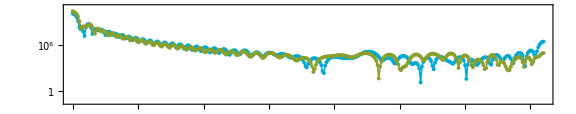

```mathematica
linearplot431FFMicro1=ListPlot[{dataFF4310DegreeLinear, dataFF4310DegreeLinearMicro},PlotMarkers->{"●",4},
                      Joined->True,
                      ScalingFunctions->"Log",
                      PlotRange->{{Automatic,Automatic},{10^(-1.5),10^(11)}},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1]&/@{MaTeX["\\varphi=0^{\\circ}"],
                                                                                                                      MaTeX["\\varphi=0^{\\circ}"]},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",4},
                                    LegendMargins->0,
                                    
                                    Spacings->0.05],{0.5,0.8}],
                      PlotStyle -> {Directive[colorsCHCM[[1]], Thickness[0.002]],Directive[greenlight30, Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{nm}^2] "],Magnification->1.05],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.05],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Large,
                      AspectRatio->2/10,
                      FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.25],
                      Evaluate[Sequence @@ plotStyling]]
```

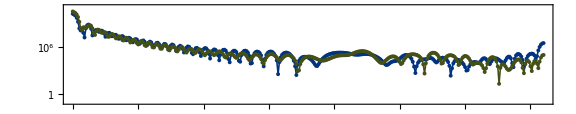

```mathematica
linearplot431FFMicro2=ListPlot[{dataFF431Pi2DegreeLinear,dataFF431Pi2DegreeLinearMicro},PlotMarkers->{"●",4},
                      Joined->True,
                      ScalingFunctions->"Log",
                      PlotRange->{{Automatic,Automatic},{10^(-1),10^(11)}},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1]&/@{MaTeX["\\varphi=90^{\\circ}"],
                                                                                                                      MaTeX["\\varphi=90^{\\circ}"]},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",4},
                                    LegendMargins->0,
                                    
                                    Spacings->0.05],{0.5,0.8}],
                      PlotStyle -> {Directive[colorsCHCM[[2]], Thickness[0.002]],Directive[greendark30, Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{nm}^2] "],Magnification->1.05],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.05],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Large,
                      AspectRatio->2/10,
                      FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.25],
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["linearplot431FFMicro1.svg",linearplot431FFMicro1]
Export["linearplot431FFMicro2.svg",linearplot431FFMicro2]
```

linearplot431FFMicro1.svg

linearplot431FFMicro2.svg

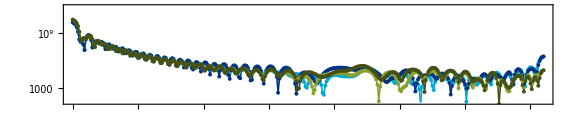

```mathematica
linearplot431FFMicro=ListPlot[{dataFF4310DegreeLinear, dataFF431Pi2DegreeLinear,
                                                        dataFF4310DegreeLinearMicro,dataFF431Pi2DegreeLinearMicro},PlotMarkers->{"●",4},
                      Joined->True,
                      ScalingFunctions->"Log",
                      PlotRange->{{Automatic,Automatic},{10^(1.5),10^(11.8)}},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1]&/@{MaTeX["\\varphi=0^{\\circ}"],MaTeX["\\varphi=90^{\\circ}"],
                                                                                                                      MaTeX["\\varphi=0^{\\circ}"],MaTeX["\\varphi=90^{\\circ}"]},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",4},
                                    LegendMargins->0,
                                    
                                    Spacings->0.05],{0.5,0.8}],
                      PlotStyle -> {Directive[colorsCHCM[[1]], Thickness[0.002]],Directive[colorsCHCM[[2]], Thickness[0.002]],
                                            
                                                Directive[greenlight30, Thickness[0.002]],Directive[greendark30, Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{nm}^2] "],Magnification->1.05],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.05],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Large,
                      AspectRatio->2/10,
                      FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.25],
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["linearplot431FFMicro.svg",linearplot431FFMicro]
```

linearplot431FFMicro.svg

```mathematica
polarplot431FFCompEsfMicro=ListPolarPlot[
 {dataFF4310, dataFF431Pi2,dataFF4310Micro,dataFF431Pi2Micro},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 2, 4, 6, 8, 10}
 },

 PlotLegends -> Placed[SwatchLegend[
   {
    Style[MaTeX["\\varphi=0"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=\\pi/2"], Magnification -> 1.7],
    Style[MaTeX["\\varphi=0"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=\\pi/2"], Magnification -> 1.7]
   }],
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},
Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-15.0,0},{-15.0,10}}],

 (* ticks *)
   Table[   Line[{     {-15.3,r},     { -15.0,r}   }],
   {r,0,10,2}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-15.15,r},{ -15,r}}], {r,0,10,0.5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-16.5,r} ], {r,0,10,2}],
     Text[Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{dB}] "], Magnification->1.8],  {-16,12.0} ]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {bluelight30,bluedark30,greenlight30,greendark30}),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 12
]
```

-Graphics-

```mathematica
Export["polarplot431FFComEsfMicro.svg",polarplot431FFCompEsfMicro]
```

polarplot431FFComEsfMicro.svg

```mathematica
cf431Micro = ColorMapSuite["navia"];
```

```mathematica
plotMicro431axes=SphericalPlot3D[
 fInterp431Micro[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
 PlotPoints -> 100,

 ColorFunction -> Function[{x, y, z, th, ph},
   cf431Micro[
     Rescale[
       fInterp431Micro[th, ph],
       {min431Micro, max431Micro}
     ]
   ]
 ],
 ColorFunctionScaling -> False,

 PlotStyle -> Opacity[1],
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 Mesh -> False,
 Exclusions -> None,

PlotLegends -> BarLegend[
 {cf431Micro, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,\\,\\, "],Magnification->1.4]
],
 LabelStyle -> {
   Black,
   FontFamily -> "Latin Modern Roman 10",
   FontSize -> 18
 },
  ViewPoint -> {1, 12, 0}, 
  ViewVertical -> {0, -1, 0}
]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
plotMicro431noaxes0=SphericalPlot3D[fInterp431Micro[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
  ColorFunction -> Function[{x, y, z, th, ph},
   cf431Micro[
     Rescale[
       fInterp431Micro[th, ph],
       {min431Esf, max431Esf}
     ]
   ]
 ],
 
 ColorFunctionScaling -> False,
 
 PlotPoints -> 100,
 Boxed -> False,
 Axes -> False,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 
PlotLegends -> Placed[BarLegend[
 {cf431Micro, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["(\\text{d}C_{\\text{sca}}/\\text{d}\\Omega)/(\\text{d}C_{\\text{sca}}/\\text{d}\\Omega)_{\\text{max}}\\,\\,\\, "],
 Magnification->1.6]
],Top],
   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->20},
   ViewPoint -> {1, 1, 0}, 
  ViewVertical -> {0, -1, 0}
 ];

planeX=ParametricPlot3D[{0,y,z},{y,-100,100},{z,-100,120},PlotStyle->Directive[greendark30,Opacity[0.25]],Mesh->None];

planeY=ParametricPlot3D[{x,0,z},{x,-100,100},{z,-100,120},PlotStyle->Directive[RGBColor[0/255,212/255,0/255],Opacity[0.15]],Mesh->None];

plotMicro431noaxes=Show[plotMicro431noaxes0,planeX,planeY,PlotRange->All]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Export["FFdistribution431_Micro.svg",plotMicro431noaxes]
Export["FFdistribution431axes_Micro.svg",plotMicro431axes]
```

FFdistribution431_Micro.svg

FFdistribution431axes_Micro.svg

### Cálculo de propiedades

#### Factor de anisotropía

```mathematica
fInterp431LinearMicro = Interpolation[data431LinearMicro];
CscaInt431Micro = NIntegrate[(fInterp431LinearMicro[th, phi]/(4 Pi))* Sin[th], {th, 0, Pi}, {phi, 0, 2 Pi}];

g431Micro = NIntegrate[ (fInterp431LinearMicro[th, phi]/(4 Pi))* Cos[th]*Sin[th],{th, 0, Pi},{phi, 0, 2 Pi}]/CscaInt431Micro
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.16563×10^7 and 9783.23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.03276×10^7 and 7527.43 for the integral and error estimates.

0.983728

```mathematica
CscaInt431Micro
```

8.16563×10^7

#### Correlaciones

```mathematica
fInterp431LinearMicro = Interpolation[data431LinearMicro,InterpolationOrder->1];

dataFF431Pi2DegreeLinearFrontMicro=Table[{fInterp431LinearMicro[th, Pi/2]}, {th, 0,  Pi/3,  Pi/60}];
dataFF431Pi2DegreeLinearLatMicro=Table[{fInterp431LinearMicro[th, Pi/2]}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF431Pi2DegreeLinearRetroMicro=Table[{fInterp431LinearMicro[th, Pi/2]}, {th, 2 Pi/3,  Pi,  Pi/60}];

dataFF4310DegreeLinearFrontMicro=Table[{fInterp431LinearMicro[th, 0]}, {th, 0,  Pi/3,  Pi/60}];
dataFF4310DegreeLinearLatMicro=Table[{fInterp431LinearMicro[th, 0]}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF4310DegreeLinearRetroMicro=Table[{fInterp431LinearMicro[th, 0]}, {th, 2 Pi/3,  Pi,  Pi/60}];
```

```mathematica
Correlation[dataFF4310DegreeLinearFrontMicro,dataFF431Pi2DegreeLinearFrontMicro]
Correlation[dataFF4310DegreeLinearLatMicro,dataFF431Pi2DegreeLinearLatMicro]
Correlation[dataFF4310DegreeLinearRetroMicro,dataFF431Pi2DegreeLinearRetroMicro]
```

{{1.}}

{{0.555576}}

{{0.761603}}

```mathematica
fInterp541Linear = Interpolation[data541Linear,InterpolationOrder->1];

dataFF541Pi2DegreeLinearFront=Table[{fInterp541Linear[th, Pi/2]}, {th, 0,  Pi/3,  Pi/60}];
dataFF541Pi2DegreeLinearLat=Table[{fInterp541Linear[th, Pi/2]}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF541Pi2DegreeLinearRetro=Table[{fInterp541Linear[th, Pi/2]}, {th, 2 Pi/3,  Pi,  Pi/60}];

dataFF5410DegreeLinearFront=Table[{fInterp541Linear[th, 0]}, {th, 0,  Pi/3,  Pi/60}];
dataFF5410DegreeLinearLat=Table[{fInterp541Linear[th, 0]}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF5410DegreeLinearRetro=Table[{fInterp541Linear[th, 0]}, {th, 2 Pi/3,  Pi,  Pi/60}];
```

```mathematica
Correlation[dataFF5410DegreeLinearFront,dataFF541Pi2DegreeLinearFront]
Correlation[dataFF5410DegreeLinearLat,dataFF541Pi2DegreeLinearLat]
Correlation[dataFF5410DegreeLinearRetro,dataFF541Pi2DegreeLinearRetro]
```

{{1.}}

{{0.499152}}

{{0.999226}}

```mathematica
fInterp573Linear = Interpolation[data573Linear,InterpolationOrder->1];

dataFF573Pi2DegreeLinearFront=Table[{fInterp573Linear[th, Pi/2]}, {th, 0,  Pi/3,  Pi/60}];
dataFF573Pi2DegreeLinearLat=Table[{fInterp573Linear[th, Pi/2]}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF573Pi2DegreeLinearRetro=Table[{fInterp573Linear[th, Pi/2]}, {th, 2 Pi/3,  Pi,  Pi/60}];

dataFF5730DegreeLinearFront=Table[{fInterp573Linear[th, 0]}, {th, 0,  Pi/3,  Pi/60}];
dataFF5730DegreeLinearLat=Table[{fInterp573Linear[th, 0]}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF5730DegreeLinearRetro=Table[{fInterp573Linear[th, 0]}, {th, 2 Pi/3,  Pi,  Pi/60}];
```

```mathematica
Correlation[dataFF5730DegreeLinearFront,dataFF573Pi2DegreeLinearFront]
Correlation[dataFF5730DegreeLinearLat,dataFF573Pi2DegreeLinearLat]
Correlation[dataFF5730DegreeLinearRetro,dataFF573Pi2DegreeLinearRetro]
```

{{1.}}

{{0.70656}}

{{0.997843}}

#### Contribuciones integradas

```mathematica
CscaInt431Front0Micro = NIntegrate[(fInterp431LinearMicro[th, 0]/(4 Pi))* Sin[th], {th, 0, Pi/3}]
CscaInt431FrontPi2Micro = NIntegrate[(fInterp431LinearMicro[th, Pi/2]/(4 Pi))* Sin[th], {th, 0, Pi/3}]

CscaInt431FrontDifMicro=100*Abs[CscaInt431Front0Micro-CscaInt431FrontPi2Micro]/CscaInt431Front0Micro

CscaInt431Lat0Micro = NIntegrate[(fInterp431LinearMicro[th, 0]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]
CscaInt431LatPi2Micro = NIntegrate[(fInterp431LinearMicro[th, Pi/2]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]

CscaInt431LatDifMicro=100*Abs[CscaInt431Lat0Micro-CscaInt431LatPi2Micro]/CscaInt431Lat0Micro

CscaInt431Retro0Micro = NIntegrate[(fInterp431LinearMicro[th, 0]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]
CscaInt431RetroPi2Micro = NIntegrate[(fInterp431LinearMicro[th, Pi/2]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]

CscaInt431RetroDifMicro=100*Abs[CscaInt431Retro0Micro-CscaInt431RetroPi2Micro]/CscaInt431Retro0Micro
```

1.33009×10^7

1.32451×10^7

0.419803

43220.

71836.4

66.2111

13333.8

22425.6

68.186

```mathematica
CscaInt431Front0Micro/(Pi * 3450^2)
CscaInt431Lat0Micro/(Pi * 3450^2)
CscaInt431Retro0Micro/(Pi * 3450^2)

CscaInt431FrontPi2Micro/(Pi * 3450^2)
CscaInt431LatPi2Micro/(Pi * 3450^2)
CscaInt431RetroPi2Micro/(Pi * 3450^2)
```

0.355707

0.00115584

0.000356588

0.354214

0.00192113

0.00059973

```mathematica
Mean[{(CscaInt431Front0Micro/CscaInt431Front0),(CscaInt431FrontPi2Micro/CscaInt431FrontPi2)}]
Mean[{CscaInt431Lat0Micro/CscaInt431Front0,CscaInt431LatPi2Micro/CscaInt431LatPi2}]
Mean[{CscaInt431Retro0Micro/CscaInt431Retro0,CscaInt431RetroPi2Micro/CscaInt431RetroPi2}]
```

1.66655

0.377301

1.60563

```mathematica
5894.70
```

```mathematica
CscaInt541Front0 = NIntegrate[(fInterp541Linear[th, 0]/(4 Pi))* Sin[th], {th, 0, Pi/3}]
CscaInt541Front2Pi = NIntegrate[(fInterp541Linear[th, 2 Pi]/(4 Pi))* Sin[th], {th, 0, Pi/3}]

CscaInt541FrontDif=Abs[CscaInt541Front0-CscaInt541Front2Pi]


CscaInt541Lat0 = NIntegrate[(fInterp541Linear[th, 0]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]
CscaInt541Lat2Pi = NIntegrate[(fInterp541Linear[th, 2 Pi]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]

CscaInt541LatDif=Abs[CscaInt541Lat0-CscaInt541Lat2Pi]


CscaInt541Retro0 = NIntegrate[(fInterp541Linear[th, 0]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]
CscaInt541Retro2Pi = NIntegrate[(fInterp541Linear[th, 2 Pi]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]

CscaInt541RetroDif=Abs[CscaInt541Retro0-CscaInt541Retro2Pi]
```

1.91037×10^7

1.91047×10^7

991.495

66659.

66615.

44.0036

47648.4

47643.7

4.68099

```mathematica
CscaInt573Front0 = NIntegrate[(fInterp573Linear[th, 0]/(4 Pi))* Sin[th], {th, 0, Pi/3}]
CscaInt573Front2Pi = NIntegrate[(fInterp573Linear[th, 2 Pi]/(4 Pi))* Sin[th], {th, 0, Pi/3}]

CscaInt573FrontDif=Abs[CscaInt573Front0-CscaInt573Front2Pi]

CscaInt573Lat0 = NIntegrate[(fInterp573Linear[th, 0]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]
CscaInt573Lat2Pi = NIntegrate[(fInterp573Linear[th, 2 Pi]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]

CscaInt573LatDif=Abs[CscaInt573Lat0-CscaInt573Lat2Pi]


CscaInt573Retro0 = NIntegrate[(fInterp573Linear[th, 0]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]
CscaInt573Retro2Pi = NIntegrate[(fInterp573Linear[th, 2 Pi]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]

CscaInt573RetroDif=Abs[CscaInt573Retro0-CscaInt573Retro2Pi]
```

2.05433×10^7

2.05422×10^7

1038.82

56327.8

56211.3

116.437

10872.

10872.

0.0174434

#### Desfase

```mathematica
interv1=Table[{x, x + 3}, {x, 0, 57,3}]
```

{{0,3},{3,6},{6,9},{9,12},{12,15},{15,18},{18,21},{21,24},{24,27},{27,30},{30,33},{33,36},{36,39},{39,42},{42,45},{45,48},{48,51},{51,54},{54,57},{57,60}}

{{120,125},{125,130},{130,135},{135,140},{140,145},{145,150},{150,155},{155,160},{160,165},{165,170},{170,175}}

```mathematica
f4310Micro[x_]:=fInterp431LinearMicro[x*Pi/180,0]/(4 Pi)
 f4310Eri[x_]:=fInterp431Linear[x*Pi/180,0]/(4 Pi)
 locf4310Micro=GoldenSectionSearchMax[f4310Micro, #1, #2, 0.0005] & @@@ interv1
 locf4310Eri=GoldenSectionSearchMax[f4310Eri, #1, #2, 0.0005] & @@@ interv1
 
 Mean[Abs[locf4310Micro-locf4310Eri]]
```

{0.000679656,4.49958,6.50003,9.50003,12.0007,15.0007,20.5,23.5,26.5,29.0006,32.0006,35.5,38.5,41.5005,42.0007,45.0007,48.5,52.4996,56.5,57.0007}

{0.000679656,5.99932,6.00068,10.9998,13.9998,16.4996,19.0002,21.5,24.0007,29.5,32.5,34.9998,37.9998,40.9998,43.9998,47.5,50.5,53.9993,54.0007,57.9994}

1.34958

```mathematica
f431Pi2Micro[x_]:=fInterp431LinearMicro[x*Pi/180,Pi/2]/(4 Pi)
 f431Pi2Eri[x_]:=fInterp431Linear[x*Pi/180,Pi/2]/(4 Pi)
 locf431Pi2Micro=GoldenSectionSearchMax[f431Pi2Micro, #1, #2, 0.0005] & @@@ interv1
 locf431Pi2Eri=GoldenSectionSearchMax[f431Pi2Eri, #1, #2, 0.0005] & @@@ interv1
 
 Mean[Abs[locf431Pi2Micro-locf431Pi2Eri]]
```

{0.000679656,4.49958,6.50003,9.50003,12.0007,15.0007,20.5,23.5,26.5,28.9998,31.9998,34.9998,38.5,41.5,44.9993,45.0007,48.5,52.0002,55.9998,59.9993}

{0.000679656,5.99932,6.00068,10.9998,13.9998,16.4996,19.0002,21.5,24.0007,29.5,32.5,34.9998,37.9998,40.9998,43.9998,47.5,50.5005,51.0007,54.0007,58.0002}

{0.,1.49974,0.499353,1.49974,1.99909,1.4989,1.49974,1.99993,2.49929,0.500193,0.500193,0.,0.500193,0.500193,0.999547,2.49929,2.00045,0.999547,1.99909,1.99909}

1.27468

## Esfera con 28.7 g/dl

```mathematica
datos287=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Funciones_dielectricas\\epsEritrocitosData28lambda.csv"];
datosEPS287 =Interpolation[Transpose[{datos287[[All,1]],Sqrt[datos287[[All,2]]+ I datos287[[All,3]]]}]]
```

InterpolatingFunction[…]

```mathematica
datos30=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Funciones_dielectricas\\epsEritrocitosData30lambda.csv"];
datosEPS30 =Interpolation[Transpose[{datos30[[All,1]],Sqrt[datos30[[All,2]]+ I datos30[[All,3]]]}]]

datos34=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Funciones_dielectricas\\epsEritrocitosData34lambda.csv"];
datosEPS34 =Interpolation[Transpose[{datos34[[All,1]],Sqrt[datos34[[All,2]]+ I datos34[[All,3]]]}]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
eriQabsMicro=Table[{λ,mieQabs[datosEPS287[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
eriQscaMicro=Table[{λ,mieQsca[datosEPS287[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
eriQextMicro=Table[{λ,mieQext[datosEPS287[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
```

```mathematica
eriQabsMicro2=Table[{λ,mieQabs[datosEPS287[λ],Sqrt[1.823],2458,λ][[4]]},{λ,400,600,1}];
eriQscaMicro2=Table[{λ,mieQsca[datosEPS287[λ],Sqrt[1.823],2458,λ][[4]]},{λ,400,600,1}];
eriQextMicro2=Table[{λ,mieQext[datosEPS287[λ],Sqrt[1.823],2458,λ][[4]]},{λ,400,600,1}];
```

```mathematica
eriQabsMicro3=Table[{λ,mieQabs[datosEPS30[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
eriQscaMicro3=Table[{λ,mieQsca[datosEPS30[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
eriQextMicro3=Table[{λ,mieQext[datosEPS30[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
```

```mathematica
eriQabsMicro4=Table[{λ,mieQabs[datosEPS287[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
eriQscaMicro4=Table[{λ,mieQsca[datosEPS30[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
eriQextMicro4=Table[{λ,mieQext[datosEPS30[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
```

```mathematica
eriQabsMicro5=Table[{λ,mieQabs[datosEPS30[λ],Sqrt[1.823],2458,λ][[4]]},{λ,400,600,1}];
eriQscaMicro5=Table[{λ,mieQsca[datosEPS30[λ],Sqrt[1.823],2458,λ][[4]]},{λ,400,600,1}];
eriQextMicro5=Table[{λ,mieQext[datosEPS30[λ],Sqrt[1.823],2458,λ][[4]]},{λ,400,600,1}];
```

```mathematica
eriCextMicro5=Table[{λ,mieQext[datosEPS30[λ],Sqrt[1.823],2458,λ][[3]]},{λ,400,600,1}];
```

```mathematica
eriCextEsf287=Table[{λ,mieQext[datosEPS287[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,800,1}];
eriCextEsf306=Table[{λ,mieQext[datosEPS30[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,800,1}];
```

```mathematica
eriCscaEsf287=Table[{λ,mieQsca[datosEPS287[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,800,1}];
eriCscaEsf306=Table[{λ,mieQsca[datosEPS30[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,800,1}];
eriCabsEsf287=Table[{λ,mieQabs[datosEPS287[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,800,1}];
eriCabsEsf306=Table[{λ,mieQabs[datosEPS30[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,800,1}];
```

```mathematica
eriCextEsf34=Table[{λ,mieQext[datosEPS34[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,800,1}];
eriCscaEsf34=Table[{λ,mieQsca[datosEPS34[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,800,1}];
eriCabsEsf34=Table[{λ,mieQabs[datosEPS34[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,800,1}];
```

```mathematica
RGBColor[85/255,153/255,1]
RGBColor[255/255,42/255,42/155]
```

RGBColor[Rational[1, 3], Rational[3, 5], 1]

RGBColor[1, Rational[14, 85], Rational[42, 155]]

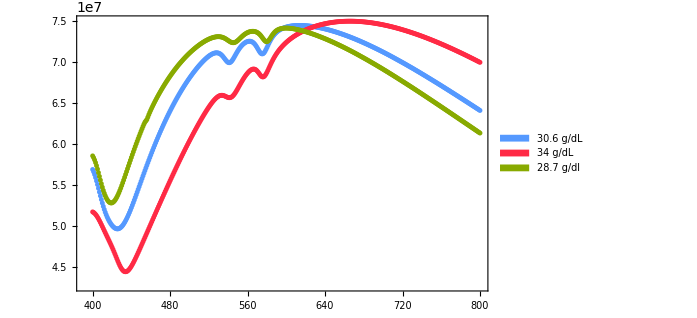

```mathematica
esferaDifConcentracion=ListPlot[{eriCextEsf306,eriCextEsf34,eriCextEsf287},PlotMarkers->{"●",5},
                      Joined->True,
                      
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]],
                                          Directive[RGBColor[136/255,170/255,0/155], Thickness[0.002]],
                                                          },
                       PlotLegends->SwatchLegend[{"30.6 g/dL","34 g/dL","28.7 g/dl"}],
                      FrameLabel->{{Style[MaTeX["C_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                   ImagePadding->{{100,10},{60,20}},
                      Evaluate[Sequence @@ plotStyling]]
```

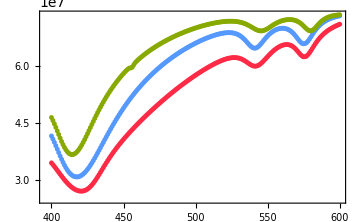

```mathematica
esferaDifConcentracionCsca=ListPlot[{eriCscaEsf306,eriCscaEsf34,eriCscaEsf287},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{2.5*10^(7),Automatic}},
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]],
                                          Directive[RGBColor[136/255,170/255,0/155], Thickness[0.002]],
                                                          },
                      FrameLabel->{{Style[MaTeX["C_{\\text{sca}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                   ImagePadding->{{100,10},{60,20}},
                      Evaluate[Sequence @@ plotStyling]]
```

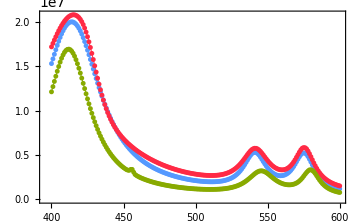

```mathematica
esferaDifConcentracionCabs=ListPlot[{eriCabsEsf306,eriCabsEsf34,eriCabsEsf287},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{0,Automatic}},
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]],
                                          Directive[RGBColor[136/255,170/255,0/155], Thickness[0.002]],
                                                          },
                      FrameLabel->{{Style[MaTeX["C_{\\text{abs}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                   ImagePadding->{{100,10},{60,20}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
eriCextEsf287Normal=Table[{λ,mieQext[datosEPS287[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCextEsf287Grande=Table[{λ,mieQext[datosEPS287[λ],Sqrt[1.823],2800,λ][[3]]},{λ,400,600,1}];
eriCextEsf287Pequena=Table[{λ,mieQext[datosEPS287[λ],Sqrt[1.823],2458,λ][[3]]},{λ,400,600,1}];

eriCabsEsf287Normal=Table[{λ,mieQabs[datosEPS287[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCabsEsf287Grande=Table[{λ,mieQabs[datosEPS287[λ],Sqrt[1.823],2800,λ][[3]]},{λ,400,600,1}];
eriCabsEsf287Pequena=Table[{λ,mieQabs[datosEPS287[λ],Sqrt[1.823],2458,λ][[3]]},{λ,400,600,1}];

eriCscaEsf287Normal=Table[{λ,mieQsca[datosEPS287[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCscaEsf287Grande=Table[{λ,mieQsca[datosEPS287[λ],Sqrt[1.823],2800,λ][[3]]},{λ,400,600,1}];
eriCscaEsf287Pequena=Table[{λ,mieQsca[datosEPS287[λ],Sqrt[1.823],2458,λ][[3]]},{λ,400,600,1}];
```

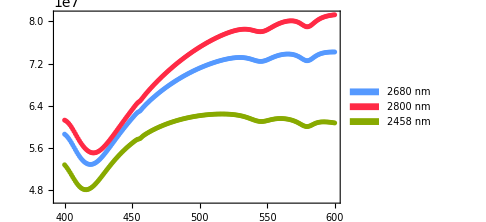

```mathematica
esferaDifConcentracion=ListPlot[{eriCextEsf287Normal,eriCextEsf287Grande,eriCextEsf287Pequena},PlotMarkers->{"●",5},
                      Joined->True,
                      
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]],
                                          Directive[RGBColor[136/255,170/255,0/155], Thickness[0.002]],
                                                          },
                      FrameLabel->{{Style[MaTeX["C_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotLegends->SwatchLegend[{"2680 nm","2800 nm", "2458 nm"}],
                      ImageSize->Medium,
                   ImagePadding->{{100,10},{60,20}},
                      Evaluate[Sequence @@ plotStyling]]
```

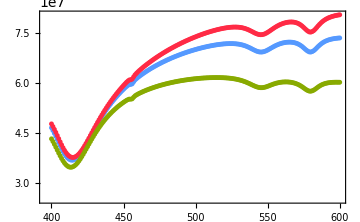

```mathematica
esferaDifConcentracionCsca=ListPlot[{eriCscaEsf287Normal,eriCscaEsf287Grande,eriCscaEsf287Pequena},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{2.5*10^(7),Automatic}},
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]],
                                          Directive[RGBColor[136/255,170/255,0/155], Thickness[0.002]],
                                                          },
                      FrameLabel->{{Style[MaTeX["C_{\\text{sca}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                   ImagePadding->{{100,10},{60,20}},
                      Evaluate[Sequence @@ plotStyling]]
```

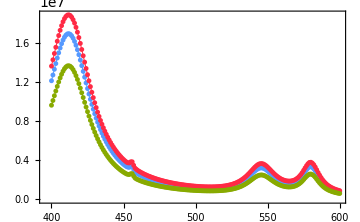

```mathematica
esferaDifConcentracionCabs=ListPlot[{eriCabsEsf287Normal,eriCabsEsf287Grande,eriCabsEsf287Pequena},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{0,Automatic}},
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]],
                                          Directive[RGBColor[136/255,170/255,0/155], Thickness[0.002]],
                                                          },
                      FrameLabel->{{Style[MaTeX["C_{\\text{abs}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                   ImagePadding->{{100,10},{60,20}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
eriCextEsf287Normal0=Table[{λ,mieQext[datosEPS30[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCextEsf287Grande0=Table[{λ,mieQext[datosEPS34[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCextEsf287Pequena0=Table[{λ,mieQext[datosEPS287[λ],Sqrt[1.823],2458,λ][[3]]},{λ,400,600,1}];

eriCabsEsf287Normal0=Table[{λ,mieQabs[datosEPS30[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCabsEsf287Grande0=Table[{λ,mieQabs[datosEPS34[λ],Sqrt[1.823],2800,λ][[3]]},{λ,400,600,1}];
eriCabsEsf287Pequena0=Table[{λ,mieQabs[datosEPS287[λ],Sqrt[1.823],2458,λ][[3]]},{λ,400,600,1}];

eriCscaEsf287Normal0=Table[{λ,mieQsca[datosEPS30[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCscaEsf287Grande0=Table[{λ,mieQsca[datosEPS34[λ],Sqrt[1.823],2800,λ][[3]]},{λ,400,600,1}];
eriCscaEsf287Pequena0=Table[{λ,mieQsca[datosEPS287[λ],Sqrt[1.823],2458,λ][[3]]},{λ,400,600,1}];
```

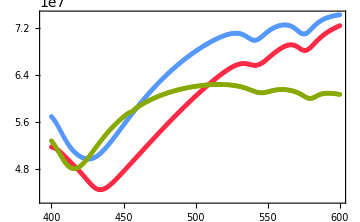

```mathematica
esferaDifConcentracion=ListPlot[{eriCextEsf287Normal0,eriCextEsf287Grande0,eriCextEsf287Pequena0},PlotMarkers->{"●",5},
                      Joined->True,
                      
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]],
                                          Directive[RGBColor[136/255,170/255,0/155], Thickness[0.002]],
                                                          },
                      FrameLabel->{{Style[MaTeX["C_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                   ImagePadding->{{100,10},{60,20}},
                      Evaluate[Sequence @@ plotStyling]]
```

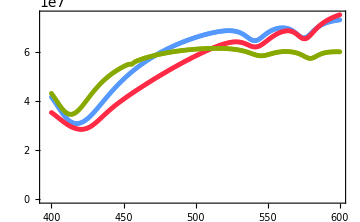

```mathematica
esferaDifConcentracion=ListPlot[{eriCscaEsf287Normal0,eriCscaEsf287Grande0,eriCscaEsf287Pequena0},PlotMarkers->{"●",5},
                      Joined->True,
                      
                      PlotStyle -> {Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],Directive[RGBColor[255/255,42/255,42/155], Thickness[0.002]],
                                          Directive[RGBColor[136/255,170/255,0/155], Thickness[0.002]],
                                                          },
                      FrameLabel->{{Style[MaTeX["C_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                   ImagePadding->{{100,10},{60,20}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
eriCextEsf287Normal0=Table[{λ,mieQext[datosEPS30[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCextEsf287Pequena0=Table[{λ,mieQext[datosEPS287[λ],Sqrt[1.823],2458,λ][[3]]},{λ,400,600,1}];
```

```mathematica
eriCextEsf287Normal1=Table[{λ,mieQext[datosEPS30[λ],Sqrt[1.823],2458,λ][[3]]},{λ,400,600,1}];
eriCextEsf287Pequena1=Table[{λ,mieQext[datosEPS287[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
```

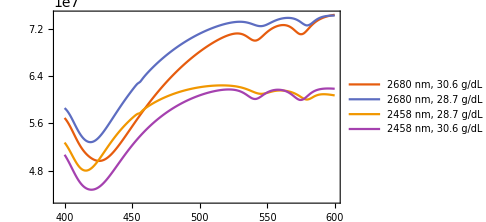

```mathematica
ListPlot[{eriCextEsf287Normal0,eriCextEsf287Pequena1,eriCextEsf287Pequena0,eriCextEsf287Normal1},PlotLegends->{"2680 nm, 30.6 g/dL","2680 nm, 28.7 g/dL",
                                                                                        "2458 nm, 28.7 g/dL","2458 nm, 30.6 g/dL"},
        FrameLabel->{{Style[MaTeX["C_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                              Joined->True,
                      ImageSize->Medium,
                   ImagePadding->{{100,10},{60,20}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
2*N[Pi*(2680)^2]
```

4.51284×10^7

```mathematica
Sqrt[1.8397]
```

1.35636

```mathematica
microcitoRISanoCsca=Transpose[{Range[400,600,50],{61687147.464449,81430085.932434,112128031.64544,124488051.38518,133987723.08950}}];
microcitoCsca=Transpose[{Range[400,600,50],{71787361.06,96982033.75,121543045.2,129870780.8,135586675.5}}];
sanoCsca=Transpose[{Range[400,600,50],{47815557.07,64217970.55,101812168.8,123587462.9,143280544.3}}];
sanoRIMicrocito=Transpose[{Range[400,600,50],{55431222.93964,80694431.180606,115972682.54650,134652780.27062,150111447.44318}}];
```

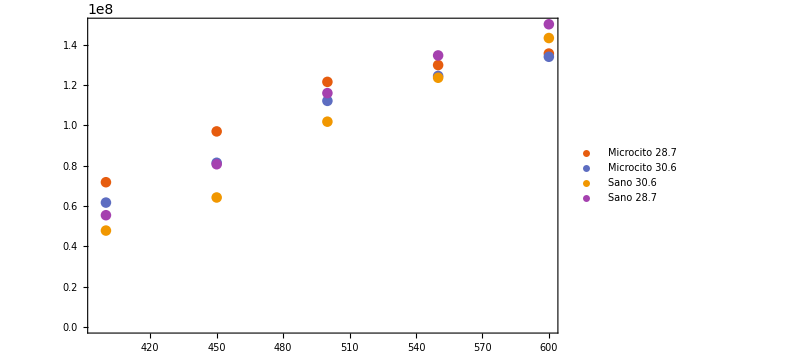

```mathematica
ListPlot[{microcitoCsca,microcitoRISanoCsca,sanoCsca,sanoRIMicrocito},PlotLegends->{"Microcito 28.7","Microcito 30.6",
                                                                                        "Sano 30.6","Sano 28.7"},
        FrameLabel->{{Style[MaTeX["C_{\\text{sca}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                              
                      ImageSize->Medium,
                   ImagePadding->{{100,10},{60,20}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
datosEPS287[λ]
```

```mathematica
eriCextEsf287Real=Table[{λ,mieQext[1.41896,Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCextEsf306Real=Table[{λ,mieQext[1.42267,Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCextEsf34Real=Table[{λ,mieQext[1.4305328606724161,Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCabsEsf287Real=Table[{λ,mieQabs[1.41896,Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCabsEsf306Real=Table[{λ,mieQabs[1.42267,Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCabsEsf34Real=Table[{λ,mieQabs[1.4305328,Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCscaEsf287Real=Table[{λ,mieQsca[1.41896,Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCscaEsf306Real=Table[{λ,mieQsca[1.42267,Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCscaEsf34Real=Table[{λ,mieQsca[1.4305328606724161,Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
```

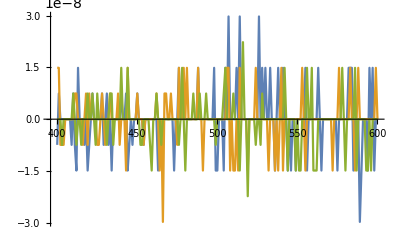

```mathematica
ListLinePlot[{eriCabsEsf287Real,eriCabsEsf306Real,eriCabsEsf34Real}]
```

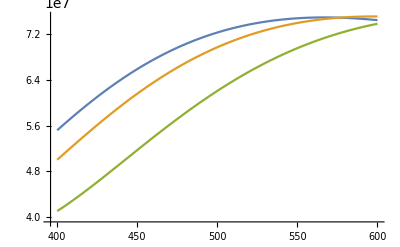

```mathematica
ListLinePlot[{eriCextEsf287Real,eriCextEsf306Real,eriCextEsf34Real}]
```

## Diferencia CST vs SolidWorks

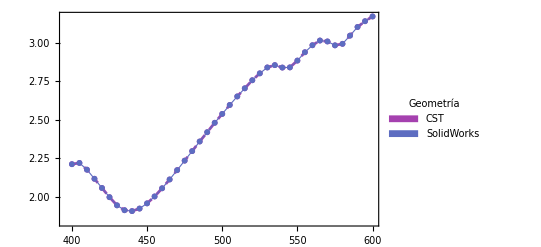

```mathematica
plotCSTSW=ListPlot[dataQext[dataQabsEsf[[#]],dataQscaEsf[[#]]]&/@{1,1},PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","SolidWorks"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.35,0.8}],
                      Joined->True,
                      PlotStyle -> {Directive[colors[[4]], Thickness[0.005],Dashed],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["CSTSW.svg",plotCSTSW]
```

CSTSW.svg

## Comparación

```mathematica
front0=Transpose[{{1,2,3},{CscaInt431Front0/(Pi * 3750^2)*10^1,CscaInt431Front0Esf/(Pi * 2680^2)*10^1,CscaInt431Front0Micro/(Pi * 3450^2)*10^1}}]
lat0=Transpose[{{1,2,3},{CscaInt431Lat0/(Pi * 3750^2)*10^(4),CscaInt431Lat0Esf/(Pi * 2680^2)*10^(4),CscaInt431Lat0Micro/(Pi * 3450^2)*10^(4)}}]
retro0=Transpose[{{1,2,3},{CscaInt431Retro0/(Pi * 3750^2)*10^(4),CscaInt431Retro0Esf/(Pi * 2680^2)*10^(4),CscaInt431Retro0Micro/(Pi * 3450^2)*10^(4)}}]
```

{{1,1.81717},{2,2.03046},{3,3.55707}}

{{1,11.7107},{2,7.60578},{3,11.5584}}

```mathematica
{{1,2.0104560979309123},{2,0.472500385284878},{3,3.5658757007201958}}
```

{{1,2.01046},{2,0.4725},{3,3.56588}}

```mathematica
mycolor1[x_] := If[Mod[x, 2] == 0,
   {colors[[9]],"●", 14},If[Mod[x, 3] == 0,
   {colors[[9]], "■", 18},{colors[[9]],"▲", 18}]];
mycolor2[x_] := If[Mod[x, 2] == 0,
   {colors[[10]],"●", 14},If[Mod[x, 3] == 0,
   {colors[[10]], "■", 18},{colors[[10]],"▲", 18}]];
mycolor3[x_] := If[Mod[x, 2] == 0,
   {colors[[11]],"●", 14},If[Mod[x, 3] == 0,
   {colors[[11]], "■", 18},{colors[[11]],"▲", 18}]];
```

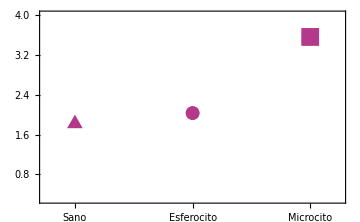

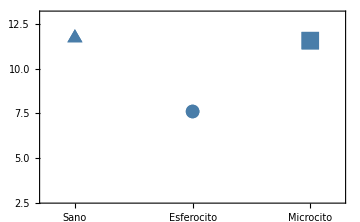

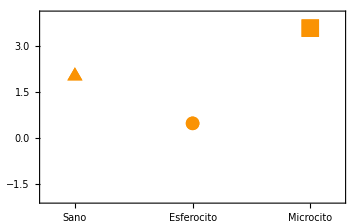

```mathematica
mycolorspec = mycolor1 /@ First /@ front0;
mycolorspec2 = mycolor2 /@ First /@ lat0;
mycolorspec3 = mycolor3 /@ First /@ retro0;
plot1=ListPlot[List /@ front0,
 PlotMarkers -> Apply[Style[#2, FontSize -> #3,#1] &,
   mycolorspec, {1}], PlotRange->{{0.75,3.25},{0.3,4}},
                      PlotStyle -> Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],
                      FrameLabel->{{Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\times 10^{1}\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\mbox{Célula}"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{{{1, Style["Sano",Magnification->1.3]}, {2, Style["Esferocito",Magnification->1.3]},  
                                                                        {3, Style["Microcito",Magnification->1.3]}},None}},
                      ImageSize->Medium,
                      Evaluate[Sequence @@ plotStyling]]
   
 plot2=ListPlot[List /@ lat0,
 PlotMarkers -> Apply[Style[#2, FontSize -> #3, #1] &,
   mycolorspec2, {1}], PlotRange->{{0.75,3.25},{2.7,13}},
                      PlotStyle -> Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],
                      FrameLabel->{{Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\times 10^{6}\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\mbox{Célula}"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{{{1, Style["Sano",Magnification->1.3]}, {2, Style["Esferocito",Magnification->1.3]},  
                                                                        {3, Style["Microcito",Magnification->1.3]}},None}},
                      ImageSize->Medium,
                      Evaluate[Sequence @@ plotStyling]]
   
plot3=ListPlot[List /@ retro0,
 PlotMarkers -> Apply[Style[#2, FontSize -> #3, #1] &,
   mycolorspec3, {1}], PlotRange->{{0.75,3.25},{-2,4}},
                      PlotStyle -> Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],
                      FrameLabel->{{Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\times 10^{6}\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\mbox{Célula}"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{{{1, Style["Sano",Magnification->1.3]}, {2, Style["Esferocito",Magnification->1.3]},  
                                                                        {3, Style["Microcito",Magnification->1.3]}},None}},
                      ImageSize->Medium,
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
list2
First /@ frontEri
```

{{1,1},{2,2},{3,3}}

{1,2,3}

```mathematica
frontlat0=Transpose[{{CscaInt431Front0/(Pi * 3750^2)*10^4,CscaInt431Front0Esf/(Pi * 2680^2)*10^4,CscaInt431Front0Micro/(Pi * 3450^2)*10^4},
                      {CscaInt431Lat0/(Pi * 3750^2)*10^(4),CscaInt431Lat0Esf/(Pi * 2680^2)*10^(4),CscaInt431Lat0Micro/(Pi * 3450^2)*10^(4)}}]
retro0={CscaInt431Retro0/(Pi * 3750^2)*10^(4),CscaInt431Retro0Esf/(Pi * 2680^2)*10^(4),CscaInt431Retro0Micro/(Pi * 3450^2)*10^(4)}


frontlatPi2=Transpose[{{CscaInt431FrontPi2/(Pi * 3750^2)*10^4,CscaInt431FrontPi2Esf/(Pi * 2680^2)*10^4,CscaInt431FrontPi2Micro/(Pi * 3450^2)*10^4},
                      {CscaInt431LatPi2/(Pi * 3750^2)*10^(4),CscaInt431LatPi2Esf/(Pi * 2680^2)*10^(4),CscaInt431LatPi2Micro/(Pi * 3450^2)*10^(4)}}]
retroPi2={CscaInt431RetroPi2/(Pi * 3750^2)*10^(4),CscaInt431RetroPi2Esf/(Pi * 2680^2)*10^(4),CscaInt431RetroPi2Micro/(Pi * 3450^2)*10^(4)}
```

{{1817.17,11.7107},{2030.46,7.60578},{3557.07,11.5584}}

{2.01046,0.4725,3.56588}

{{1788.52,21.7032},{2019.,14.4556},{3542.14,19.2113}}

{2.96843,0.90178,5.9973}

```mathematica
colorsCHCM
```

{RGBColor[0, Rational[2, 3], Rational[212, 255]],RGBColor[0, Rational[1, 5], Rational[128, 255]],RGBColor[Rational[11, 51], Rational[57, 85], Rational[40, 51]],RGBColor[1, Rational[14, 85], Rational[14, 85]],RGBColor[Rational[128, 255], 0, 0]}

```mathematica
mycolor0[x_] := If[Mod[x, CscaInt431Front0/(Pi * 3750^2)*10^4] == 0,
   {colorsCHCM[[1]],"●", 17.51},If[Mod[x, CscaInt431Front0Esf/(Pi * 2680^2)*10^4] == 0,
   {colorsCHCM[[4]], "●", 10},{colorsCHCM[[6]],"●", 18}]];
   
 mycolorPi2[x_] := If[Mod[x, CscaInt431FrontPi2/(Pi * 3750^2)*10^4] == 0,
   {colorsCHCM[[1]],"●", 14},If[Mod[x, CscaInt431FrontPi2Esf/(Pi * 2680^2)*10^4] == 0,
   {colorsCHCM[[4]], "●", 10},{colorsCHCM[[6]],"●", 18}]];
```

```mathematica
CscaInt431Front0Esf/(Pi * 2680^2)*10^4
(CscaInt431Front0/(Pi * 3750^2)*10^4)
CscaInt431Front0Micro/(Pi * 3450^2)*10^4
```

2030.46

1817.17

3557.07

```mathematica
10*(CscaInt431Front0Micro/(Pi * 3450^2)*10^4)/(CscaInt431Front0Esf/(Pi * 2680^2)*10^4)
10*(CscaInt431Front0/(Pi * 3750^2)*10^4)/(CscaInt431Front0Esf/(Pi * 2680^2)*10^4)
```

17.5186

8.94954

```mathematica
First /@ frontlat0
```

{1817.17,2030.46,3557.07}

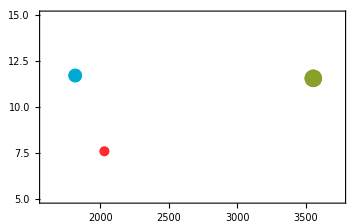

```mathematica
mycolorspec0 = mycolor0 /@ First /@ frontlat0;
plot1=ListPlot[List /@ frontlat0,
 PlotMarkers -> Apply[Style[#2, FontSize -> #3,#1] &,
   mycolorspec0, {1}], PlotRange->{{1600,3750},{5,15}},
                      
                      FrameLabel->{{Style[MaTeX["\\,\\text{SCC}\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\text{FSC}\\,[\\text{nm}^2]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                      Evaluate[Sequence @@ plotStyling]]
```

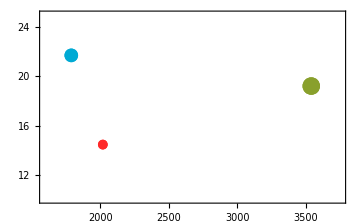

```mathematica
mycolorspecPi2 = mycolorPi2 /@ First /@ frontlatPi2;
plotPi2=ListPlot[List /@ frontlatPi2,
 PlotMarkers -> Apply[Style[#2, FontSize -> #3,#1] &,
   mycolorspecPi2, {1}], PlotRange->{{1600,3750},{10,25}},
                      
                      FrameLabel->{{Style[MaTeX["\\,\\text{SCC}\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\text{FSC}\\,[\\text{nm}^2]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                      Evaluate[Sequence @@ plotStyling]]
```